## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

```mathematica
Directory[]
```

/Users/meister/Development/cando/extensions/cando/src/mathematica

```mathematica
SetDirectory["/Users/meister/Development/Cando/extensions/cando/src/mathematica"]
```

/Users/meister/Development/cando/extensions/cando/src/mathematica

## Setup to generate code that is embeded within CANDO

```mathematica
Needs["optimizeExpressions`"]
```

```mathematica
normquatrot[x_,y_,z_,w_,tx_,ty_,tz_]:= ({{1.0-2.0y*y - 2*z*z, 2*x*y+2*w*z, 2*x*z-2*w*y, tx}, {2*x*y-2*w*z, 1-2*x*x-2*z*z, 2*y*z+2*w*x, ty}, {2*x*z+2*w*y, 2*y*z-2*w*x, 1-2*x*x-2*y*y, tz}, {0, 0, 0, 1}})
```

```mathematica
quattrans2[w_,x_,y_,z_,tx_,ty_,tz_] :=
({{w*w+x*x-y*y-z*z, 2*(-w*z+x*y), 2*(w*y+x*z), tx}, {2*(w*z+x*y), w*w-x*x+y*y-z*z, 2*(-w*x+y*z), ty}, {2*(-w*y+x*z), 2*(w*x+y*z), w*w-x*x-y*y+z*z, tz}, {0, 0, 0, w*w+x*x+y*y+z*z}})
```

```mathematica
quattrans3[w_,x_,y_,z_,tx_,ty_,tz_] :=
({{w*w+x*x-y*y-z*z, 2*(-w*z+x*y), 2*(w*y+x*z), tx}, {2*(w*z+x*y), w*w-x*x+y*y-z*z, 2*(-w*x+y*z), ty}, {2*(-w*y+x*z), 2*(w*x+y*z), w*w-x*x-y*y+z*z, tz}, {0, 0, 0, 1}})
```

```mathematica
quattrans[w_,x_,y_,z_,tx_,ty_,tz_] := quattrans3[w,x,y,z,tx,ty,tz]
```

### Define a quaternion

```mathematica
quat[a_,b_,c_,d_] := {a,b,c,d}
```

### Separate out the real/imaginary parts

```mathematica
quatreal[qv_] := qv[[1]]
```

```mathematica
quatimaginary[qv_] := {qv[[2]],qv[[3]],qv[[4]]}
```

```mathematica
quatmag[qv_] := Sqrt[qv[[1]]*qv[[1]]+qv[[2]]*qv[[2]]+qv[[3]]*qv[[3]]+qv[[4]]*qv[[4]]]
```

### Rotate a vector using a normalized quaternion

```mathematica
quatvecmul[qv_,vec_] := vec+(2.0*Cross[quatimaginary[qv],(Cross[quatimaginary[qv],vec]+quatreal[qv]*vec)])/(quatmag[qv]*quatmag[qv])
```

#### Test it

```mathematica
quatvecmul[quat[a,b,c,d],{vx,vy,vz}]
```

{vx+(2. (-c^2 vx-d^2 vx+b c vy-a d vy+a c vz+b d vz))/(a^2+b^2+c^2+d^2),vy+(2. (b c vx+a d vx-b^2 vy-d^2 vy-a b vz+c d vz))/(a^2+b^2+c^2+d^2),vz+(2. (-a c vx+b d vx+a b vy+c d vy-b^2 vz-c^2 vz))/(a^2+b^2+c^2+d^2)}

### Translate the rotated vector

```mathematica
quatmultrans[qv_,trans_,vec_] := quatvecmul[qv,vec]+trans
```

# Cylindrical rigid-body repulsion energy term using quat.v multiplication (method 2) https://en.wikipedia.org/wiki/Quaternions_and_spatial_rotation#Quaternion_rotation_operations

```mathematica
Clear[a,b,c,d,x,y,z];
```

### pki and pkf are points in the k rigid body frame and pli and plf are points in the l rigid body frame

```mathematica
pki = { pxki, pyki, pzki };
pli = { pxli,pyli,pzli};
pkf = { pxkf, pykf, pzk f};
plf = { pxlf,pylf,pzlf};
```

### plabki is pki transformed into the laboratory frame by a quaterion rotation and translation - likewise plabkf plabli plablf

```mathematica
plabki = quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},pki];
plabkf = quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},pkf];
plabli = quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},pli];
plablf = quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},plf];
```

### Calculate vectors dlabk dlabl

```mathematica
dlabk = plabkf - plabki;
dlabl = plablf - plabli;
```

### Calculate v, orthonormal vector with respect to dlabk and dlabl

```mathematica
epsilon=
w= dlabk×dlabl;
v=w/(norm[w]+epsilon)
```

(quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},{pxkf,pykf,f pzk}]-quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},{pxki,pyki,pzki}])×(quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},{pxlf,pylf,pzlf}]-quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},{pxli,pyli,pzli}])

(quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},{pxkf,pykf,f pzk}]-quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},{pxki,pyki,pzki}])×(quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},{pxlf,pylf,pzlf}]-quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},{pxli,pyli,pzli}])/norm[(quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},{pxkf,pykf,f pzk}]-quatmultrans[quat[ak,bk,ck,dk],{xk,yk,zk},{pxki,pyki,pzki}])×(quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},{pxlf,pylf,pzlf}]-quatmultrans[quat[al,bl,cl,dl],{xl,yl,zl},{pxli,pyli,pzli}])]

### Calculate line-line distance, dlabkl

```mathematica
dlabkl = (plabli- plabki).v;
```

### Calculate vector along the line-line distance, vlabkl

```mathematica
vlabkl = dlabkl *v;
```

### evaluating alpha and beta from plabki plabli dlabk dlabl vlabkl

```mathematica
alpha = (plabki[[1]]/dlabk[[1]]- plabki[[2]]/dlabk[[2]]+vlabkl[[1]]/dlabk[[1]]-vlabkl[[2]]/dlabk[[2]] -(plabli[[1]]/dlabk[[1]]- plabli[[2]]/dlabk[[2]]))/(dlabl[[1]]/dlabk[[1]]-dlabl[[2]]/dlabk[[2]])
```

```mathematica
beta = (plabli[[1]]/dlabl[[1]]- plabli[[2]]/dlabl[[2]]-(plabki[[1]]/dlabl[[1]]- plabki[[2]]/dlabl[[2]]+vlabkl[[1]]/dlabl[[1]]-vlabkl[[2]]/dlabl[[2]]))/(dlabk[[1]]/dlabl[[1]]-dlabk[[2]]/dlabl[[2]])
```

### Calculate the smoothing function along the line-line distance, vlabkl

```mathematica
g(parameter_)=1/2*(1+(2^(12-1)-(2*parameter_-1)^12)/(1+(2^(12-1)+(2*parameter_-1)^12))
```

### Define a repulsive potential for the deviation using the force constant sigma

```mathematica
small=10^-10;
```

```mathematica
CylRepEnergyFn = sigma ((dlabkl)^2+small)^-6* g(alpha)*g(beta)
```

ks (-r0+√((pxk-pxl+(2. (-ck^2 pxk-dk^2 pxk+bk ck pyk-ak dk pyk+ak ck pzk+bk dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (-cl^2 pxl-dl^2 pxl+bl cl pyl-al dl pyl+al cl pzl+bl dl pzl))/(al^2+bl^2+cl^2+dl^2)+xk-xl)^2+(pyk-pyl+(2. (bk ck pxk+ak dk pxk-bk^2 pyk-dk^2 pyk-ak bk pzk+ck dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (bl cl pxl+al dl pxl-bl^2 pyl-dl^2 pyl-al bl pzl+cl dl pzl))/(al^2+bl^2+cl^2+dl^2)+yk-yl)^2+(pzk+(2. (-ak ck pxk+bk dk pxk+ak bk pyk+ck dk pyk-bk^2 pzk-ck^2 pzk))/(ak^2+bk^2+ck^2+dk^2)-pzl-(2. (-al cl pxl+bl dl pxl+al bl pyl+cl dl pyl-bl^2 pzl-cl^2 pzl))/(al^2+bl^2+cl^2+dl^2)+zk-zl)^2))^2

```mathematica
cylrepVarNames = { 
{ak,a,I1,0},
{bk,b,I1,1},
{ck,c,I1,2},
{dk,d,I1,3},
{xk,x,I1,4},
{yk,y,I1,5},
{zk,z,I1,6},
{al,a,I2,0},
{bl,b,I2,1},
{cl,c,I2,2},
{dl,d,I2,3},
{xl,x,I2,4},
{yl,y,I2,5},
{zl,z,I2,6}
};
```

```mathematica
cylrepSetupRules = {};
AppendTo[cylrepSetupRules,CCode["CYLREP_SET_PARAMETER(sigma,sigma);"]];
AppendTo[cylrepSetupRules,CCode["CYLREP_SET_PARAMETER(I1,rigidBodyK);"]];
AppendTo[cylrepSetupRules,CCode["CYLREP_SET_PARAMETER(I2,rigidBodyL);"]];
```

```mathematica
For[i=1,i≤Length[cylrepVarNames],i++,
str = "CYLREP_SET_POSITION("<>ToString[cylrepVarNames[[i]][[1]]]<>","<>ToString[cylrepVarNames[[i]][[3]]]<>","<>ToString[cylrepVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[cylrepSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pxki,pointKi,getX());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pyki,pointKi,getY());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pzki,pointKi,getZ());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pxli,pointLi,getX());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pyli,pointLi,getY());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pzli,pointLi,getZ());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pxkf,pointKf,getX());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pykf,pointKf,getY());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pzkf,pointKf,getZ());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pxlf,pointLf,getX());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pylf,pointLf,getY());"]];
AppendTo[cylrepSetupRules, CCode["CYLREP_SET_POINT(pzlf,pointL,getZ());"]];
```

```mathematica
cylrepSetupRules//MatrixForm
```

```mathematica
({{CCode["CYLREP_SET_PARAMETER(ks,ks);"]}, {CCode["CYLREP_SET_PARAMETER(r0,r0);"]}, {CCode["CYLREP_SET_PARAMETER(I1,rigidBodyK);"]}, {CCode["CYLREP_SET_PARAMETER(I2,rigidBodyL);"]}, {CCode["CYLREP_SET_POSITION(ak,I1,0);"]}, {CCode["CYLREP_SET_POSITION(bk,I1,1);"]}, {CCode["CYLREP_SET_POSITION(ck,I1,2);"]}, {CCode["CYLREP_SET_POSITION(dk,I1,3);"]}, {CCode["CYLREP_SET_POSITION(xk,I1,4);"]}, {CCode["CYLREP_SET_POSITION(yk,I1,5);"]}, {CCode["CYLREP_SET_POSITION(zk,I1,6);"]}, {CCode["CYLREP_SET_POSITION(al,I2,0);"]}, {CCode["CYLREP_SET_POSITION(bl,I2,1);"]}, {CCode["CYLREP_SET_POSITION(cl,I2,2);"]}, {CCode["CYLREP_SET_POSITION(dl,I2,3);"]}, {CCode["CYLREP_SET_POSITION(xl,I2,4);"]}, {CCode["CYLREP_SET_POSITION(yl,I2,5);"]}, {CCode["CYLREP_SET_POSITION(zl,I2,6);"]}, {CCode["CYLREP_SET_POINT(pxk,pointK,getX());"]}, {CCode["CYLREP_SET_POINT(pyk,pointK,getY());"]}, {CCode["CYLREP_SET_POINT(pzk,pointK,getZ());"]}, {CCode["CYLREP_SET_POINT(pxl,pointL,getX());"]}, {CCode["CYLREP_SET_POINT(pyl,pointL,getY());"]}, {CCode["CYLREP_SET_POINT(pzl,pointL,getZ());"]}})
```

```mathematica
cylrepEnergyRules = {};
cylrepOutputs = {};
AppendTo[cylrepEnergyRules,Assign[Energy,CylRepEnergyFn]];
AppendTo[cylrepEnergyRules,EnergyAccumulate["CYLREP",Energy]];
AppendTo[cylrepOutputs,Energy];
```

```mathematica
cylrepEnergyRules
```

```mathematica
{ks (-r0+√((pxk-pxl+(2. (-ck^2 pxk-dk^2 pxk+bk ck pyk-ak dk pyk+ak ck pzk+bk dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (-cl^2 pxl-dl^2 pxl+bl cl pyl-al dl pyl+al cl pzl+bl dl pzl))/(al^2+bl^2+cl^2+dl^2)+xk-xl)^2+(pyk-pyl+(2. (bk ck pxk+ak dk pxk-bk^2 pyk-dk^2 pyk-ak bk pzk+ck dk pzk))/(ak^2+bk^2+ck^2+dk^2)-(2. (bl cl pxl+al dl pxl-bl^2 pyl-dl^2 pyl-al bl pzl+cl dl pzl))/(al^2+bl^2+cl^2+dl^2)+yk-yl)^2+(pzk+(2. (-ak ck pxk+bk dk pxk+ak bk pyk+ck dk pyk-bk^2 pzk-ck^2 pzk))/(ak^2+bk^2+ck^2+dk^2)-pzl-(2. (-al cl pxl+bl dl pxl+al bl pyl+cl dl pyl-bl^2 pzl-cl^2 pzl))/(al^2+bl^2+cl^2+dl^2)+zk-zl)^2))^2->Energy,CCode["CYLREP_ENERGY_ACCUMULATE(Energy);"]}
```

## Append the Gradient rules

```mathematica
cylrepForceRules = {};
```

```mathematica
AppendGradientAndForce["CYLREP",cylrepEnergyRules,cylrepOutputs,CylRepEnergyFn,cylrepVarNames];
```

```mathematica
cylrepOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

### Collect terms and convert to C code

```mathematica
cylrepAllRules ={
cylrepSetupRules,
cylrepEnergyRules};
```

```mathematica
cylrepRules = Flatten[cylrepAllRules];
```

```mathematica
cylrepRules[[4]]
```

```mathematica
CCode["CYLREP_SET_PARAMETER(I2,rigidBodyL);"]
```

```mathematica
cylrepInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

AppendTo[cylrepOutputs, cylrepDeviation];

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
cylrepPack0 = {
Name->"CYLREP",
AdditionalCDeclares->"",
DerivativeVariables->cylrepInput,
Rules->cylrepRules,
Input->cylrepInput,
Output->cylrepOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[cylrepPack0];
```

Writing finite difference debug code to: _STAPLE_debugFiniteDifference.cc

Writing debug variable declares to: _STAPLE_debugEvalDeclares.cc

Writing xml output debug code to: _STAPLE_debugEvalSerialize.cc

Writing set variables debug code to: _STAPLE_debugEvalSet.cc

cylrepPack = Block[{PrintTemporary = Print}, packOptimize[cylrepPack0]];

### Put the pedal to the metal and generate "C" code.

```mathematica
cylrepOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

```mathematica
Output/.cylrepPack
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

```mathematica
cylrepPack = packOptimize[cylrepPack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

trivialRules>> triv = {tzz409 -> tx246, tzz408 -> tx247, tzz419 -> tx248, tzz413 -> tx285, tzz416 -> tx306, tzz412 -> tx309, tzz411 -> tx343, tzz414 -> tx345, tzz415 -> tx358, tzz406 -> tx384}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

tzz413 -> tx285

tzz416 -> tx306

tzz412 -> tx309

tzz411 -> tx343

tzz414 -> tx345

tzz415 -> tx358

tzz406 -> tx384

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "STAPLE", AdditionalCDeclares → "", DerivativeVariables → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Rules → {CCode["STAPLE_SET_PARAMETER(ks,ks);"], CCode["STAPLE_SET_PARAMETER(r0,r0);"], CCode["STAPLE_SET_PARAMETER(I1,rigidBodyK);"], « 45 », -gal → fal, CCode["STAPLE_FORCE_ACCUMULATE(I2, 0, fal );"], « 18 »}, Input → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

There were no trivial rules

trivialRules>> triv = {tzz575 -> tx332, tzz574 -> tx333, tzz585 -> tx334, tzz579 -> tx365, tzz582 -> tx402, tzz578 -> tx405, tzz577 -> tx466, tzz580 -> tx468, tzz581 -> tx491, tzz573 -> tx535}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

tzz579 -> tx365

tzz582 -> tx402

tzz578 -> tx405

tzz577 -> tx466

tzz580 -> tx468

tzz581 -> tx491

tzz573 -> tx535

After removal: CCode[CYLREP_SET_PARAMETER(ks,ks);]\n\nCCode[CYLREP_SET_PARAMETER(r0,r0);]\n\nCCode[CYLREP_SET_PARAMETER(I1,rigidBodyK);]\n\nCCode[CYLREP_SET_PARAMETER(I2,rigidBodyL);]\n\nCCode[CYLREP_SET_POSITION(ak,I1,0);]\n\nCCode[CYLREP_SET_POSITION(bk,I1,1);]\n\nCCode[CYLREP_SET_POSITION(ck,I1,2);]\n\nCCode[CYLREP_SET_POSITION(dk,I1,3);]\n\nCCode[CYLREP_SET_POSITION(xk,I1,4);]\n\nCCode[CYLREP_SET_POSITION(yk,I1,5);]\n\nCCode[CYLREP_SET_POSITION(zk,I1,6);]\n\nCCode[CYLREP_SET_POSITION(al,I2,0);]\n\nCCode[CYLREP_SET_POSITION(bl,I2,1);]\n\nCCode[CYLREP_SET_POSITION(cl,I2,2);]\n\nCCode[CYLREP_SET_POSITION(dl,I2,3);]\n\nCCode[CYLREP_SET_POSITION(xl,I2,4);]\n\nCCode[CYLREP_SET_POSITION(yl,I2,5);]\n\nCCode[CYLREP_SET_POSITION(zl,I2,6);]\n\nCCode[CYLREP_SET_POINT(pxk,pointK,getX());]\n\nCCode[CYLREP_SET_POINT(pyk,pointK,getY());]\n\nCCode[CYLREP_SET_POINT(pzk,pointK,getZ());]\n\nCCode[CYLREP_SET_POINT(pxl,pointL,getX());]\n\nCCode[CYLREP_SET_POINT(pyl,pointL,getY());]\n\nCCode[CYLREP_SET_POINT(pzl,pointL,getZ());]\n\npower2[ak] -> tx278\n\npower2[al] -> tx279\n\npower2[bk] -> tx280\n\npower2[bl] -> tx281\n\npower2[ck] -> tx282\n\npower2[cl] -> tx283\n\npower2[dk] -> tx284\n\npower2[dl] -> tx285\n\n-pxk -> tzz565\n\nak ck -> tzz583\n\ntzz565 tzz583 -> tx286\n\nbk ck pxk -> tx287\n\ndk pxk -> tzz579\n\nak tzz579 -> tx288\n\nbk tzz579 -> tx289\n\n-pxl -> tzz575\n\nal cl tzz575 -> tx290\n\nbl cl pxl -> tx291\n\ndl pxl -> tzz577\n\nal tzz577 -> tx292\n\nbl tzz577 -> tx293\n\nak bk -> tzz584\n\npyk tzz584 -> tx294\n\nck pyk -> tzz582\n\nbk tzz582 -> tx295\n\n-pyk -> tzz572\n\nak dk tzz572 -> tx296\n\ndk tzz582 -> tx297\n\nal bl pyl -> tx298\n\ncl pyl -> tzz581\n\nbl tzz581 -> tx299\n\n-pyl -> tzz574\n\nal dl tzz574 -> tx300\n\ndl tzz581 -> tx301\n\n-pzk -> tzz564\n\ntzz564 tzz584 -> tx302\n\npzk tzz583 -> tx303\n\ndk pzk -> tzz578\n\nbk tzz578 -> tx304\n\nck tzz578 -> tx305\n\nbl pzl -> tzz573\n\n-(al tzz573) -> tx306\n\ncl pzl -> tzz580\n\nal tzz580 -> tx307\n\ndl tzz573 -> tx308\n\ndl tzz580 -> tx309\n\ntx280 tzz572 -> tx310\n\ntx280 tzz564 -> tx311\n\ntx281 tzz574 -> tx312\n\n-pzl -> tzz585\n\ntx281 tzz585 -> tx313\n\ntx282 tzz565 -> tx314\n\ntx282 tzz564 -> tx315\n\ntx283 tzz575 -> tx316\n\ntx283 tzz585 -> tx317\n\ntx284 tzz565 -> tx318\n\ntx284 tzz572 -> tx319\n\ntx278 + tx280 + tx282 + tx284 -> tx320\n\ntx285 tzz575 -> tx321\n\ntx285 tzz574 -> tx322\n\ntx279 + tx281 + tx283 + tx285 -> tx323\n\ntx286 + tx289 + tx294 + tx297 + tx311 + tx315 -> tx324\n\ntx290 + tx293 + tx298 + tx301 + tx313 + tx317 -> tx325\n\ntx295 + tx296 + tx303 + tx304 + tx314 + tx318 -> tx326\n\ntx287 + tx288 + tx302 + tx305 + tx310 + tx319 -> tx327\n\nreciprocal[tx320] -> tx328\n\ntx299 + tx300 + tx307 + tx308 + tx316 + tx321 -> tx329\n\ntx291 + tx292 + tx306 + tx309 + tx312 + tx322 -> tx330\n\nreciprocal[tx323] -> tx331\n\ntzz575 -> tx332\n\ntzz574 -> tx333\n\ntzz585 -> tx334\n\n2. tx328 -> tzz556\n\ntx324 tzz556 -> tx335\n\ntx326 tzz556 -> tx336\n\ntx327 tzz556 -> tx337\n\n-2. tx331 -> tzz555\n\ntx325 tzz555 -> tx338\n\ntx329 tzz555 -> tx339\n\ntx330 tzz555 -> tx340\n\n-xl -> tx341\n\n-yl -> tx342\n\n-zl -> tx343\n\npxk + tx332 + tx336 + tx339 + tx341 + xk -> tx344\n\npyk + tx333 + tx337 + tx340 + tx342 + yk -> tx345\n\npzk + tx334 + tx335 + tx338 + tx343 + zk -> tx346\n\npower2[tx344] -> tx347\n\npower2[tx345] -> tx348\n\npower2[tx346] -> tx349\n\ntx347 + tx348 + tx349 -> tx350\n\n-r0 -> tx351\n\nmysqrt[tx350] -> tx352\n\ntx351 + tx352 -> tx353\n\npower2[tx353] -> tx354\n\nks tx354 -> Energy\n\nCCode[CYLREP_ENERGY_ACCUMULATE(Energy);]\n\ntx283 tx332 -> tx355\n\ntx285 tx332 -> tx356\n\ntx281 tx333 -> tx357\n\ntx285 tx333 -> tx358\n\ntx281 tx334 -> tx359\n\ntx283 tx334 -> tx360\n\ntx299 + tx300 + tx307 + tx308 + tx355 + tx356 -> tx361\n\ntx291 + tx292 + tx306 + tx309 + tx357 + tx358 -> tx362\n\ntx290 + tx293 + tx298 + tx301 + tx359 + tx360 -> tx363\n\nck tzz565 -> tx364\n\ntzz579 -> tx365\n\nbk pyk -> tx366\n\ndk tzz572 -> tx367\n\nbk tzz564 -> tx368\n\nck pzk -> tx369\n\ntx361 tzz555 -> tx370\n\ntx362 tzz555 -> tx371\n\ntx363 tzz555 -> tx372\n\npower2[tx328] -> tx373\n\ntx364 + tx366 -> tx374\n\ntx365 + tx368 -> tx375\n\ntx367 + tx369 -> tx376\n\npxk + tx332 + tx336 + tx341 + tx370 + xk -> tx377\n\npyk + tx333 + tx337 + tx342 + tx371 + yk -> tx378\n\npzk + tx334 + tx335 + tx343 + tx372 + zk -> tx379\n\n-4. tx373 -> tzz560\n\ntx324 tzz560 -> tzz571\n\nak tzz571 -> tx380\n\ntx326 tzz560 -> tzz570\n\nak tzz570 -> tx381\n\ntx327 tzz560 -> tzz569\n\nak tzz569 -> tx382\n\ntx374 tzz556 -> tx383\n\ntx375 tzz556 -> tx384\n\ntx376 tzz556 -> tx385\n\npower2[tx377] -> tx386\n\npower2[tx378] -> tx387\n\npower2[tx379] -> tx388\n\ntx380 + tx383 -> tx389\n\ntx382 + tx384 -> tx390\n\ntx381 + tx385 -> tx391\n\ntx386 + tx387 + tx388 -> tx392\n\n2. tx379 -> tzz561\n\ntx389 tzz561 -> tx393\n\n2. tx378 -> tzz562\n\ntx390 tzz562 -> tx394\n\n2. tx377 -> tzz563\n\ntx391 tzz563 -> tx395\n\nmysqrt[tx392] -> tx396\n\nreciprocal[tx396] -> tx397\n\ntx393 + tx394 + tx395 -> tx398\n\ntx351 + tx396 -> tx399\n\ntx397 tx399 -> tzz557\n\nks tzz557 -> tzz558\n\ntx398 tzz558 -> gak\n\n-gak -> fak\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 0, fak );]\n\nck pxk -> tx400\n\nak pyk -> tx401\n\ntzz582 -> tx402\n\nak tzz564 -> tx403\n\n-2. bk pzk -> tx404\n\ntzz578 -> tx405\n\n-2. tx366 -> tx406\n\ntx365 + tx401 + tx404 -> tx407\n\ntx402 + tx405 -> tx408\n\ntx400 + tx403 + tx406 -> tx409\n\nbk tzz571 -> tx410\n\nbk tzz570 -> tx411\n\nbk tzz569 -> tx412\n\ntx407 tzz556 -> tx413\n\ntx408 tzz556 -> tx414\n\ntx409 tzz556 -> tx415\n\ntx410 + tx413 -> tx416\n\ntx411 + tx414 -> tx417\n\ntx412 + tx415 -> tx418\n\ntx416 tzz561 -> tx419\n\ntx417 tzz563 -> tx420\n\ntx418 tzz562 -> tx421\n\ntx419 + tx420 + tx421 -> tx422\n\ntx422 tzz558 -> gbk\n\n-gbk -> fbk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 1, fbk );]\n\nak tzz565 -> tx423\n\nbk pxk -> tx424\n\ndk pyk -> tx425\n\nak pzk -> tx426\n\n-2. tx369 -> tx427\n\n-2. tx400 -> tx428\n\ntx405 + tx424 -> tx429\n\ntx423 + tx425 + tx427 -> tx430\n\ntx366 + tx426 + tx428 -> tx431\n\nck tzz571 -> tx432\n\nck tzz570 -> tx433\n\nck tzz569 -> tx434\n\ntx429 tzz556 -> tx435\n\ntx430 tzz556 -> tx436\n\ntx431 tzz556 -> tx437\n\ntx434 + tx435 -> tx438\n\ntx432 + tx436 -> tx439\n\ntx433 + tx437 -> tx440\n\ntx438 tzz562 -> tx441\n\ntx439 tzz561 -> tx442\n\ntx440 tzz563 -> tx443\n\ntx441 + tx442 + tx443 -> tx444\n\ntx444 tzz558 -> gck\n\n-gck -> fck\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 2, fck );]\n\nak pxk -> tx445\n\nbk pzk -> tx446\n\n-2. tx365 -> tx447\n\n-tx401 -> tx448\n\n-2. tx425 -> tx449\n\ntx402 + tx424 -> tx450\n\ntx446 + tx447 + tx448 -> tx451\n\ntx369 + tx445 + tx449 -> tx452\n\ndk tzz571 -> tx453\n\ndk tzz570 -> tx454\n\ndk tzz569 -> tx455\n\ntx450 tzz556 -> tx456\n\ntx451 tzz556 -> tx457\n\ntx452 tzz556 -> tx458\n\ntx453 + tx456 -> tx459\n\ntx454 + tx457 -> tx460\n\ntx455 + tx458 -> tx461\n\ntx459 tzz561 -> tx462\n\ntx460 tzz563 -> tx463\n\ntx461 tzz562 -> tx464\n\ntx462 + tx463 + tx464 -> tx465\n\ntx465 tzz558 -> gdk\n\n-gdk -> fdk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz558 tzz563 -> gxk\n\n-gxk -> fxk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz558 tzz562 -> gyk\n\n-gyk -> fyk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz558 tzz561 -> gzk\n\n-gzk -> fzk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz577 -> tx466\n\nbl pyl -> tx467\n\ntzz580 -> tx468\n\ncl tx332 -> tx469\n\ndl tx333 -> tx470\n\nbl tx334 -> tx471\n\npower2[tx331] -> tx472\n\ntx467 + tx469 -> tx473\n\ntx468 + tx470 -> tx474\n\ntx466 + tx471 -> tx475\n\n4. tx472 -> tzz559\n\ntx361 tzz559 -> tzz568\n\nal tzz568 -> tx476\n\ntx362 tzz559 -> tzz567\n\nal tzz567 -> tx477\n\ntx363 tzz559 -> tzz566\n\nal tzz566 -> tx478\n\ntx473 tzz555 -> tx479\n\ntx474 tzz555 -> tx480\n\ntx475 tzz555 -> tx481\n\ntx478 + tx479 -> tx482\n\ntx476 + tx480 -> tx483\n\ntx477 + tx481 -> tx484\n\ntx482 tzz561 -> tx485\n\ntx483 tzz563 -> tx486\n\ntx484 tzz562 -> tx487\n\ntx485 + tx486 + tx487 -> tx488\n\ntx488 tzz558 -> gal\n\n-gal -> fal\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 0, fal );]\n\ncl pxl -> tx489\n\nal pyl -> tx490\n\ntzz581 -> tx491\n\n-2. tzz573 -> tx492\n\ndl pzl -> tx493\n\nal tx334 -> tx494\n\n-2. tx467 -> tx495\n\ntx466 + tx490 + tx492 -> tx496\n\ntx491 + tx493 -> tx497\n\ntx489 + tx494 + tx495 -> tx498\n\nbl tzz568 -> tx499\n\nbl tzz567 -> tx500\n\nbl tzz566 -> tx501\n\ntx496 tzz555 -> tx502\n\ntx497 tzz555 -> tx503\n\ntx498 tzz555 -> tx504\n\ntx501 + tx502 -> tx505\n\ntx499 + tx503 -> tx506\n\ntx500 + tx504 -> tx507\n\ntx505 tzz561 -> tx508\n\ntx506 tzz563 -> tx509\n\ntx507 tzz562 -> tx510\n\ntx508 + tx509 + tx510 -> tx511\n\ntx511 tzz558 -> gbl\n\n-gbl -> fbl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 1, fbl );]\n\nbl pxl -> tx512\n\ndl pyl -> tx513\n\nal pzl -> tx514\n\nal tx332 -> tx515\n\n-2. tx468 -> tx516\n\n-2. tx489 -> tx517\n\ntx493 + tx512 -> tx518\n\ntx513 + tx515 + tx516 -> tx519\n\ntx467 + tx514 + tx517 -> tx520\n\ncl tzz568 -> tx521\n\ncl tzz567 -> tx522\n\ncl tzz566 -> tx523\n\ntx518 tzz555 -> tx524\n\ntx519 tzz555 -> tx525\n\ntx520 tzz555 -> tx526\n\ntx522 + tx524 -> tx527\n\ntx523 + tx525 -> tx528\n\ntx521 + tx526 -> tx529\n\ntx527 tzz562 -> tx530\n\ntx528 tzz561 -> tx531\n\ntx529 tzz563 -> tx532\n\ntx530 + tx531 + tx532 -> tx533\n\ntx533 tzz558 -> gcl\n\n-gcl -> fcl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nal pxl -> tx534\n\ntzz573 -> tx535\n\nal tx333 -> tx536\n\n-2. tx466 -> tx537\n\n-2. tx513 -> tx538\n\ntx491 + tx512 -> tx539\n\ntx535 + tx536 + tx537 -> tx540\n\ntx468 + tx534 + tx538 -> tx541\n\ndl tzz568 -> tx542\n\ndl tzz567 -> tx543\n\ndl tzz566 -> tx544\n\ntx539 tzz555 -> tx545\n\ntx540 tzz555 -> tx546\n\ntx541 tzz555 -> tx547\n\ntx544 + tx545 -> tx548\n\ntx542 + tx546 -> tx549\n\ntx543 + tx547 -> tx550\n\ntx548 tzz561 -> tx551\n\ntx549 tzz563 -> tx552\n\ntx550 tzz562 -> tx553\n\ntx551 + tx552 + tx553 -> tx554\n\ntx554 tzz558 -> gdl\n\n-gdl -> fdl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tzz558 -> tzz576\n\ntx377 tzz576 -> gxl\n\n-gxl -> fxl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 4, fxl );]\n\ntx378 tzz576 -> gyl\n\n-gyl -> fyl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 5, fyl );]\n\ntx379 tzz576 -> gzl\n\n-gzl -> fzl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz575 -> tx332, tzz574 -> tx333, tzz585 -> tx334, tzz579 -> tx365, tzz582 -> tx402, tzz578 -> tx405, tzz577 -> tx466, tzz580 -> tx468, tzz581 -> tx491, tzz573 -> tx535}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

tzz579 -> tx365

tzz582 -> tx402

tzz578 -> tx405

tzz577 -> tx466

tzz580 -> tx468

tzz581 -> tx491

tzz573 -> tx535

After removal: CCode[CYLREP_SET_PARAMETER(ks,ks);]\n\nCCode[CYLREP_SET_PARAMETER(r0,r0);]\n\nCCode[CYLREP_SET_PARAMETER(I1,rigidBodyK);]\n\nCCode[CYLREP_SET_PARAMETER(I2,rigidBodyL);]\n\nCCode[CYLREP_SET_POSITION(ak,I1,0);]\n\nCCode[CYLREP_SET_POSITION(bk,I1,1);]\n\nCCode[CYLREP_SET_POSITION(ck,I1,2);]\n\nCCode[CYLREP_SET_POSITION(dk,I1,3);]\n\nCCode[CYLREP_SET_POSITION(xk,I1,4);]\n\nCCode[CYLREP_SET_POSITION(yk,I1,5);]\n\nCCode[CYLREP_SET_POSITION(zk,I1,6);]\n\nCCode[CYLREP_SET_POSITION(al,I2,0);]\n\nCCode[CYLREP_SET_POSITION(bl,I2,1);]\n\nCCode[CYLREP_SET_POSITION(cl,I2,2);]\n\nCCode[CYLREP_SET_POSITION(dl,I2,3);]\n\nCCode[CYLREP_SET_POSITION(xl,I2,4);]\n\nCCode[CYLREP_SET_POSITION(yl,I2,5);]\n\nCCode[CYLREP_SET_POSITION(zl,I2,6);]\n\nCCode[CYLREP_SET_POINT(pxk,pointK,getX());]\n\nCCode[CYLREP_SET_POINT(pyk,pointK,getY());]\n\nCCode[CYLREP_SET_POINT(pzk,pointK,getZ());]\n\nCCode[CYLREP_SET_POINT(pxl,pointL,getX());]\n\nCCode[CYLREP_SET_POINT(pyl,pointL,getY());]\n\nCCode[CYLREP_SET_POINT(pzl,pointL,getZ());]\n\npower2[ak] -> tx278\n\npower2[al] -> tx279\n\npower2[bk] -> tx280\n\npower2[bl] -> tx281\n\npower2[ck] -> tx282\n\npower2[cl] -> tx283\n\npower2[dk] -> tx284\n\npower2[dl] -> tx285\n\n-pxk -> tzz565\n\nak ck -> tzz583\n\ntzz565 tzz583 -> tx286\n\nbk ck pxk -> tx287\n\ndk pxk -> tzz579\n\nak tzz579 -> tx288\n\nbk tzz579 -> tx289\n\n-pxl -> tzz575\n\nal cl tzz575 -> tx290\n\nbl cl pxl -> tx291\n\ndl pxl -> tzz577\n\nal tzz577 -> tx292\n\nbl tzz577 -> tx293\n\nak bk -> tzz584\n\npyk tzz584 -> tx294\n\nck pyk -> tzz582\n\nbk tzz582 -> tx295\n\n-pyk -> tzz572\n\nak dk tzz572 -> tx296\n\ndk tzz582 -> tx297\n\nal bl pyl -> tx298\n\ncl pyl -> tzz581\n\nbl tzz581 -> tx299\n\n-pyl -> tzz574\n\nal dl tzz574 -> tx300\n\ndl tzz581 -> tx301\n\n-pzk -> tzz564\n\ntzz564 tzz584 -> tx302\n\npzk tzz583 -> tx303\n\ndk pzk -> tzz578\n\nbk tzz578 -> tx304\n\nck tzz578 -> tx305\n\nbl pzl -> tzz573\n\n-(al tzz573) -> tx306\n\ncl pzl -> tzz580\n\nal tzz580 -> tx307\n\ndl tzz573 -> tx308\n\ndl tzz580 -> tx309\n\ntx280 tzz572 -> tx310\n\ntx280 tzz564 -> tx311\n\ntx281 tzz574 -> tx312\n\n-pzl -> tzz585\n\ntx281 tzz585 -> tx313\n\ntx282 tzz565 -> tx314\n\ntx282 tzz564 -> tx315\n\ntx283 tzz575 -> tx316\n\ntx283 tzz585 -> tx317\n\ntx284 tzz565 -> tx318\n\ntx284 tzz572 -> tx319\n\ntx278 + tx280 + tx282 + tx284 -> tx320\n\ntx285 tzz575 -> tx321\n\ntx285 tzz574 -> tx322\n\ntx279 + tx281 + tx283 + tx285 -> tx323\n\ntx286 + tx289 + tx294 + tx297 + tx311 + tx315 -> tx324\n\ntx290 + tx293 + tx298 + tx301 + tx313 + tx317 -> tx325\n\ntx295 + tx296 + tx303 + tx304 + tx314 + tx318 -> tx326\n\ntx287 + tx288 + tx302 + tx305 + tx310 + tx319 -> tx327\n\nreciprocal[tx320] -> tx328\n\ntx299 + tx300 + tx307 + tx308 + tx316 + tx321 -> tx329\n\ntx291 + tx292 + tx306 + tx309 + tx312 + tx322 -> tx330\n\nreciprocal[tx323] -> tx331\n\ntzz575 -> tx332\n\ntzz574 -> tx333\n\ntzz585 -> tx334\n\n2. tx328 -> tzz556\n\ntx324 tzz556 -> tx335\n\ntx326 tzz556 -> tx336\n\ntx327 tzz556 -> tx337\n\n-2. tx331 -> tzz555\n\ntx325 tzz555 -> tx338\n\ntx329 tzz555 -> tx339\n\ntx330 tzz555 -> tx340\n\n-xl -> tx341\n\n-yl -> tx342\n\n-zl -> tx343\n\npxk + tx332 + tx336 + tx339 + tx341 + xk -> tx344\n\npyk + tx333 + tx337 + tx340 + tx342 + yk -> tx345\n\npzk + tx334 + tx335 + tx338 + tx343 + zk -> tx346\n\npower2[tx344] -> tx347\n\npower2[tx345] -> tx348\n\npower2[tx346] -> tx349\n\ntx347 + tx348 + tx349 -> tx350\n\n-r0 -> tx351\n\nmysqrt[tx350] -> tx352\n\ntx351 + tx352 -> tx353\n\npower2[tx353] -> tx354\n\nks tx354 -> Energy\n\nCCode[CYLREP_ENERGY_ACCUMULATE(Energy);]\n\ntx283 tx332 -> tx355\n\ntx285 tx332 -> tx356\n\ntx281 tx333 -> tx357\n\ntx285 tx333 -> tx358\n\ntx281 tx334 -> tx359\n\ntx283 tx334 -> tx360\n\ntx299 + tx300 + tx307 + tx308 + tx355 + tx356 -> tx361\n\ntx291 + tx292 + tx306 + tx309 + tx357 + tx358 -> tx362\n\ntx290 + tx293 + tx298 + tx301 + tx359 + tx360 -> tx363\n\nck tzz565 -> tx364\n\ntzz579 -> tx365\n\nbk pyk -> tx366\n\ndk tzz572 -> tx367\n\nbk tzz564 -> tx368\n\nck pzk -> tx369\n\ntx361 tzz555 -> tx370\n\ntx362 tzz555 -> tx371\n\ntx363 tzz555 -> tx372\n\npower2[tx328] -> tx373\n\ntx364 + tx366 -> tx374\n\ntx365 + tx368 -> tx375\n\ntx367 + tx369 -> tx376\n\npxk + tx332 + tx336 + tx341 + tx370 + xk -> tx377\n\npyk + tx333 + tx337 + tx342 + tx371 + yk -> tx378\n\npzk + tx334 + tx335 + tx343 + tx372 + zk -> tx379\n\n-4. tx373 -> tzz560\n\ntx324 tzz560 -> tzz571\n\nak tzz571 -> tx380\n\ntx326 tzz560 -> tzz570\n\nak tzz570 -> tx381\n\ntx327 tzz560 -> tzz569\n\nak tzz569 -> tx382\n\ntx374 tzz556 -> tx383\n\ntx375 tzz556 -> tx384\n\ntx376 tzz556 -> tx385\n\npower2[tx377] -> tx386\n\npower2[tx378] -> tx387\n\npower2[tx379] -> tx388\n\ntx380 + tx383 -> tx389\n\ntx382 + tx384 -> tx390\n\ntx381 + tx385 -> tx391\n\ntx386 + tx387 + tx388 -> tx392\n\n2. tx379 -> tzz561\n\ntx389 tzz561 -> tx393\n\n2. tx378 -> tzz562\n\ntx390 tzz562 -> tx394\n\n2. tx377 -> tzz563\n\ntx391 tzz563 -> tx395\n\nmysqrt[tx392] -> tx396\n\nreciprocal[tx396] -> tx397\n\ntx393 + tx394 + tx395 -> tx398\n\ntx351 + tx396 -> tx399\n\ntx397 tx399 -> tzz557\n\nks tzz557 -> tzz558\n\ntx398 tzz558 -> gak\n\n-gak -> fak\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 0, fak );]\n\nck pxk -> tx400\n\nak pyk -> tx401\n\ntzz582 -> tx402\n\nak tzz564 -> tx403\n\n-2. bk pzk -> tx404\n\ntzz578 -> tx405\n\n-2. tx366 -> tx406\n\ntx365 + tx401 + tx404 -> tx407\n\ntx402 + tx405 -> tx408\n\ntx400 + tx403 + tx406 -> tx409\n\nbk tzz571 -> tx410\n\nbk tzz570 -> tx411\n\nbk tzz569 -> tx412\n\ntx407 tzz556 -> tx413\n\ntx408 tzz556 -> tx414\n\ntx409 tzz556 -> tx415\n\ntx410 + tx413 -> tx416\n\ntx411 + tx414 -> tx417\n\ntx412 + tx415 -> tx418\n\ntx416 tzz561 -> tx419\n\ntx417 tzz563 -> tx420\n\ntx418 tzz562 -> tx421\n\ntx419 + tx420 + tx421 -> tx422\n\ntx422 tzz558 -> gbk\n\n-gbk -> fbk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 1, fbk );]\n\nak tzz565 -> tx423\n\nbk pxk -> tx424\n\ndk pyk -> tx425\n\nak pzk -> tx426\n\n-2. tx369 -> tx427\n\n-2. tx400 -> tx428\n\ntx405 + tx424 -> tx429\n\ntx423 + tx425 + tx427 -> tx430\n\ntx366 + tx426 + tx428 -> tx431\n\nck tzz571 -> tx432\n\nck tzz570 -> tx433\n\nck tzz569 -> tx434\n\ntx429 tzz556 -> tx435\n\ntx430 tzz556 -> tx436\n\ntx431 tzz556 -> tx437\n\ntx434 + tx435 -> tx438\n\ntx432 + tx436 -> tx439\n\ntx433 + tx437 -> tx440\n\ntx438 tzz562 -> tx441\n\ntx439 tzz561 -> tx442\n\ntx440 tzz563 -> tx443\n\ntx441 + tx442 + tx443 -> tx444\n\ntx444 tzz558 -> gck\n\n-gck -> fck\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 2, fck );]\n\nak pxk -> tx445\n\nbk pzk -> tx446\n\n-2. tx365 -> tx447\n\n-tx401 -> tx448\n\n-2. tx425 -> tx449\n\ntx402 + tx424 -> tx450\n\ntx446 + tx447 + tx448 -> tx451\n\ntx369 + tx445 + tx449 -> tx452\n\ndk tzz571 -> tx453\n\ndk tzz570 -> tx454\n\ndk tzz569 -> tx455\n\ntx450 tzz556 -> tx456\n\ntx451 tzz556 -> tx457\n\ntx452 tzz556 -> tx458\n\ntx453 + tx456 -> tx459\n\ntx454 + tx457 -> tx460\n\ntx455 + tx458 -> tx461\n\ntx459 tzz561 -> tx462\n\ntx460 tzz563 -> tx463\n\ntx461 tzz562 -> tx464\n\ntx462 + tx463 + tx464 -> tx465\n\ntx465 tzz558 -> gdk\n\n-gdk -> fdk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz558 tzz563 -> gxk\n\n-gxk -> fxk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz558 tzz562 -> gyk\n\n-gyk -> fyk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz558 tzz561 -> gzk\n\n-gzk -> fzk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz577 -> tx466\n\nbl pyl -> tx467\n\ntzz580 -> tx468\n\ncl tx332 -> tx469\n\ndl tx333 -> tx470\n\nbl tx334 -> tx471\n\npower2[tx331] -> tx472\n\ntx467 + tx469 -> tx473\n\ntx468 + tx470 -> tx474\n\ntx466 + tx471 -> tx475\n\n4. tx472 -> tzz559\n\ntx361 tzz559 -> tzz568\n\nal tzz568 -> tx476\n\ntx362 tzz559 -> tzz567\n\nal tzz567 -> tx477\n\ntx363 tzz559 -> tzz566\n\nal tzz566 -> tx478\n\ntx473 tzz555 -> tx479\n\ntx474 tzz555 -> tx480\n\ntx475 tzz555 -> tx481\n\ntx478 + tx479 -> tx482\n\ntx476 + tx480 -> tx483\n\ntx477 + tx481 -> tx484\n\ntx482 tzz561 -> tx485\n\ntx483 tzz563 -> tx486\n\ntx484 tzz562 -> tx487\n\ntx485 + tx486 + tx487 -> tx488\n\ntx488 tzz558 -> gal\n\n-gal -> fal\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 0, fal );]\n\ncl pxl -> tx489\n\nal pyl -> tx490\n\ntzz581 -> tx491\n\n-2. tzz573 -> tx492\n\ndl pzl -> tx493\n\nal tx334 -> tx494\n\n-2. tx467 -> tx495\n\ntx466 + tx490 + tx492 -> tx496\n\ntx491 + tx493 -> tx497\n\ntx489 + tx494 + tx495 -> tx498\n\nbl tzz568 -> tx499\n\nbl tzz567 -> tx500\n\nbl tzz566 -> tx501\n\ntx496 tzz555 -> tx502\n\ntx497 tzz555 -> tx503\n\ntx498 tzz555 -> tx504\n\ntx501 + tx502 -> tx505\n\ntx499 + tx503 -> tx506\n\ntx500 + tx504 -> tx507\n\ntx505 tzz561 -> tx508\n\ntx506 tzz563 -> tx509\n\ntx507 tzz562 -> tx510\n\ntx508 + tx509 + tx510 -> tx511\n\ntx511 tzz558 -> gbl\n\n-gbl -> fbl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 1, fbl );]\n\nbl pxl -> tx512\n\ndl pyl -> tx513\n\nal pzl -> tx514\n\nal tx332 -> tx515\n\n-2. tx468 -> tx516\n\n-2. tx489 -> tx517\n\ntx493 + tx512 -> tx518\n\ntx513 + tx515 + tx516 -> tx519\n\ntx467 + tx514 + tx517 -> tx520\n\ncl tzz568 -> tx521\n\ncl tzz567 -> tx522\n\ncl tzz566 -> tx523\n\ntx518 tzz555 -> tx524\n\ntx519 tzz555 -> tx525\n\ntx520 tzz555 -> tx526\n\ntx522 + tx524 -> tx527\n\ntx523 + tx525 -> tx528\n\ntx521 + tx526 -> tx529\n\ntx527 tzz562 -> tx530\n\ntx528 tzz561 -> tx531\n\ntx529 tzz563 -> tx532\n\ntx530 + tx531 + tx532 -> tx533\n\ntx533 tzz558 -> gcl\n\n-gcl -> fcl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nal pxl -> tx534\n\ntzz573 -> tx535\n\nal tx333 -> tx536\n\n-2. tx466 -> tx537\n\n-2. tx513 -> tx538\n\ntx491 + tx512 -> tx539\n\ntx535 + tx536 + tx537 -> tx540\n\ntx468 + tx534 + tx538 -> tx541\n\ndl tzz568 -> tx542\n\ndl tzz567 -> tx543\n\ndl tzz566 -> tx544\n\ntx539 tzz555 -> tx545\n\ntx540 tzz555 -> tx546\n\ntx541 tzz555 -> tx547\n\ntx544 + tx545 -> tx548\n\ntx542 + tx546 -> tx549\n\ntx543 + tx547 -> tx550\n\ntx548 tzz561 -> tx551\n\ntx549 tzz563 -> tx552\n\ntx550 tzz562 -> tx553\n\ntx551 + tx552 + tx553 -> tx554\n\ntx554 tzz558 -> gdl\n\n-gdl -> fdl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tzz558 -> tzz576\n\ntx377 tzz576 -> gxl\n\n-gxl -> fxl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 4, fxl );]\n\ntx378 tzz576 -> gyl\n\n-gyl -> fyl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 5, fyl );]\n\ntx379 tzz576 -> gzl\n\n-gzl -> fzl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz575 -> tx332, tzz574 -> tx333, tzz585 -> tx334, tzz579 -> tx365, tzz582 -> tx402, tzz578 -> tx405, tzz577 -> tx466, tzz580 -> tx468, tzz581 -> tx491, tzz573 -> tx535}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz575 -> tx332

tzz574 -> tx333

tzz585 -> tx334

tzz579 -> tx365

tzz582 -> tx402

tzz578 -> tx405

tzz577 -> tx466

tzz580 -> tx468

tzz581 -> tx491

tzz573 -> tx535

After removal: CCode[CYLREP_SET_PARAMETER(ks,ks);]\n\nCCode[CYLREP_SET_PARAMETER(r0,r0);]\n\nCCode[CYLREP_SET_PARAMETER(I1,rigidBodyK);]\n\nCCode[CYLREP_SET_PARAMETER(I2,rigidBodyL);]\n\nCCode[CYLREP_SET_POSITION(ak,I1,0);]\n\nCCode[CYLREP_SET_POSITION(bk,I1,1);]\n\nCCode[CYLREP_SET_POSITION(ck,I1,2);]\n\nCCode[CYLREP_SET_POSITION(dk,I1,3);]\n\nCCode[CYLREP_SET_POSITION(xk,I1,4);]\n\nCCode[CYLREP_SET_POSITION(yk,I1,5);]\n\nCCode[CYLREP_SET_POSITION(zk,I1,6);]\n\nCCode[CYLREP_SET_POSITION(al,I2,0);]\n\nCCode[CYLREP_SET_POSITION(bl,I2,1);]\n\nCCode[CYLREP_SET_POSITION(cl,I2,2);]\n\nCCode[CYLREP_SET_POSITION(dl,I2,3);]\n\nCCode[CYLREP_SET_POSITION(xl,I2,4);]\n\nCCode[CYLREP_SET_POSITION(yl,I2,5);]\n\nCCode[CYLREP_SET_POSITION(zl,I2,6);]\n\nCCode[CYLREP_SET_POINT(pxk,pointK,getX());]\n\nCCode[CYLREP_SET_POINT(pyk,pointK,getY());]\n\nCCode[CYLREP_SET_POINT(pzk,pointK,getZ());]\n\nCCode[CYLREP_SET_POINT(pxl,pointL,getX());]\n\nCCode[CYLREP_SET_POINT(pyl,pointL,getY());]\n\nCCode[CYLREP_SET_POINT(pzl,pointL,getZ());]\n\npower2[ak] -> tx278\n\npower2[al] -> tx279\n\npower2[bk] -> tx280\n\npower2[bl] -> tx281\n\npower2[ck] -> tx282\n\npower2[cl] -> tx283\n\npower2[dk] -> tx284\n\npower2[dl] -> tx285\n\n-pxk -> tzz565\n\nak ck -> tzz583\n\ntzz565 tzz583 -> tx286\n\nbk ck pxk -> tx287\n\ndk pxk -> tzz579\n\nak tzz579 -> tx288\n\nbk tzz579 -> tx289\n\n-pxl -> tzz575\n\nal cl tzz575 -> tx290\n\nbl cl pxl -> tx291\n\ndl pxl -> tzz577\n\nal tzz577 -> tx292\n\nbl tzz577 -> tx293\n\nak bk -> tzz584\n\npyk tzz584 -> tx294\n\nck pyk -> tzz582\n\nbk tzz582 -> tx295\n\n-pyk -> tzz572\n\nak dk tzz572 -> tx296\n\ndk tzz582 -> tx297\n\nal bl pyl -> tx298\n\ncl pyl -> tzz581\n\nbl tzz581 -> tx299\n\n-pyl -> tzz574\n\nal dl tzz574 -> tx300\n\ndl tzz581 -> tx301\n\n-pzk -> tzz564\n\ntzz564 tzz584 -> tx302\n\npzk tzz583 -> tx303\n\ndk pzk -> tzz578\n\nbk tzz578 -> tx304\n\nck tzz578 -> tx305\n\nbl pzl -> tzz573\n\n-(al tzz573) -> tx306\n\ncl pzl -> tzz580\n\nal tzz580 -> tx307\n\ndl tzz573 -> tx308\n\ndl tzz580 -> tx309\n\ntx280 tzz572 -> tx310\n\ntx280 tzz564 -> tx311\n\ntx281 tzz574 -> tx312\n\n-pzl -> tzz585\n\ntx281 tzz585 -> tx313\n\ntx282 tzz565 -> tx314\n\ntx282 tzz564 -> tx315\n\ntx283 tzz575 -> tx316\n\ntx283 tzz585 -> tx317\n\ntx284 tzz565 -> tx318\n\ntx284 tzz572 -> tx319\n\ntx278 + tx280 + tx282 + tx284 -> tx320\n\ntx285 tzz575 -> tx321\n\ntx285 tzz574 -> tx322\n\ntx279 + tx281 + tx283 + tx285 -> tx323\n\ntx286 + tx289 + tx294 + tx297 + tx311 + tx315 -> tx324\n\ntx298 + tx301 -> tzz599\n\ntx293 + tzz599 -> tzz600\n\ntx290 + tzz600 -> tzz603\n\ntx313 + tx317 + tzz603 -> tx325\n\ntx295 + tx296 + tx303 + tx304 + tx314 + tx318 -> tx326\n\ntx287 + tx288 + tx302 + tx305 + tx310 + tx319 -> tx327\n\nreciprocal[tx320] -> tx328\n\ntx307 + tx308 -> tzz595\n\ntx300 + tzz595 -> tzz597\n\ntx299 + tzz597 -> tzz598\n\ntx316 + tx321 + tzz598 -> tx329\n\ntx306 + tx309 -> tzz596\n\ntx292 + tzz596 -> tzz601\n\ntx291 + tzz601 -> tzz602\n\ntx312 + tx322 + tzz602 -> tx330\n\nreciprocal[tx323] -> tx331\n\ntzz575 -> tx332\n\ntzz574 -> tx333\n\ntzz585 -> tx334\n\n2. tx328 -> tzz556\n\ntx324 tzz556 -> tx335\n\ntx326 tzz556 -> tx336\n\ntx327 tzz556 -> tx337\n\n-2. tx331 -> tzz555\n\ntx325 tzz555 -> tx338\n\ntx329 tzz555 -> tx339\n\ntx330 tzz555 -> tx340\n\n-xl -> tx341\n\n-yl -> tx342\n\n-zl -> tx343\n\ntx341 + xk -> tzz588\n\ntx336 + tzz588 -> tzz590\n\ntx332 + tzz590 -> tzz594\n\npxk + tzz594 -> tzz606\n\ntx339 + tzz606 -> tx344\n\ntx342 + yk -> tzz587\n\ntx337 + tzz587 -> tzz589\n\ntx333 + tzz589 -> tzz593\n\npyk + tzz593 -> tzz605\n\ntx340 + tzz605 -> tx345\n\ntx343 + zk -> tzz586\n\ntx335 + tzz586 -> tzz591\n\ntx334 + tzz591 -> tzz592\n\npzk + tzz592 -> tzz604\n\ntx338 + tzz604 -> tx346\n\npower2[tx344] -> tx347\n\npower2[tx345] -> tx348\n\npower2[tx346] -> tx349\n\ntx347 + tx348 + tx349 -> tx350\n\n-r0 -> tx351\n\nmysqrt[tx350] -> tx352\n\ntx351 + tx352 -> tx353\n\npower2[tx353] -> tx354\n\nks tx354 -> Energy\n\nCCode[CYLREP_ENERGY_ACCUMULATE(Energy);]\n\ntx283 tx332 -> tx355\n\ntx285 tx332 -> tx356\n\ntx281 tx333 -> tx357\n\ntx285 tx333 -> tx358\n\ntx281 tx334 -> tx359\n\ntx283 tx334 -> tx360\n\ntx355 + tx356 + tzz598 -> tx361\n\ntx357 + tx358 + tzz602 -> tx362\n\ntx359 + tx360 + tzz603 -> tx363\n\nck tzz565 -> tx364\n\ntzz579 -> tx365\n\nbk pyk -> tx366\n\ndk tzz572 -> tx367\n\nbk tzz564 -> tx368\n\nck pzk -> tx369\n\ntx361 tzz555 -> tx370\n\ntx362 tzz555 -> tx371\n\ntx363 tzz555 -> tx372\n\npower2[tx328] -> tx373\n\ntx364 + tx366 -> tx374\n\ntx365 + tx368 -> tx375\n\ntx367 + tx369 -> tx376\n\ntx370 + tzz606 -> tx377\n\ntx371 + tzz605 -> tx378\n\ntx372 + tzz604 -> tx379\n\n-4. tx373 -> tzz560\n\ntx324 tzz560 -> tzz571\n\nak tzz571 -> tx380\n\ntx326 tzz560 -> tzz570\n\nak tzz570 -> tx381\n\ntx327 tzz560 -> tzz569\n\nak tzz569 -> tx382\n\ntx374 tzz556 -> tx383\n\ntx375 tzz556 -> tx384\n\ntx376 tzz556 -> tx385\n\npower2[tx377] -> tx386\n\npower2[tx378] -> tx387\n\npower2[tx379] -> tx388\n\ntx380 + tx383 -> tx389\n\ntx382 + tx384 -> tx390\n\ntx381 + tx385 -> tx391\n\ntx386 + tx387 + tx388 -> tx392\n\n2. tx379 -> tzz561\n\ntx389 tzz561 -> tx393\n\n2. tx378 -> tzz562\n\ntx390 tzz562 -> tx394\n\n2. tx377 -> tzz563\n\ntx391 tzz563 -> tx395\n\nmysqrt[tx392] -> tx396\n\nreciprocal[tx396] -> tx397\n\ntx393 + tx394 + tx395 -> tx398\n\ntx351 + tx396 -> tx399\n\ntx397 tx399 -> tzz557\n\nks tzz557 -> tzz558\n\ntx398 tzz558 -> gak\n\n-gak -> fak\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 0, fak );]\n\nck pxk -> tx400\n\nak pyk -> tx401\n\ntzz582 -> tx402\n\nak tzz564 -> tx403\n\n-2. bk pzk -> tx404\n\ntzz578 -> tx405\n\n-2. tx366 -> tx406\n\ntx365 + tx401 + tx404 -> tx407\n\ntx402 + tx405 -> tx408\n\ntx400 + tx403 + tx406 -> tx409\n\nbk tzz571 -> tx410\n\nbk tzz570 -> tx411\n\nbk tzz569 -> tx412\n\ntx407 tzz556 -> tx413\n\ntx408 tzz556 -> tx414\n\ntx409 tzz556 -> tx415\n\ntx410 + tx413 -> tx416\n\ntx411 + tx414 -> tx417\n\ntx412 + tx415 -> tx418\n\ntx416 tzz561 -> tx419\n\ntx417 tzz563 -> tx420\n\ntx418 tzz562 -> tx421\n\ntx419 + tx420 + tx421 -> tx422\n\ntx422 tzz558 -> gbk\n\n-gbk -> fbk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 1, fbk );]\n\nak tzz565 -> tx423\n\nbk pxk -> tx424\n\ndk pyk -> tx425\n\nak pzk -> tx426\n\n-2. tx369 -> tx427\n\n-2. tx400 -> tx428\n\ntx405 + tx424 -> tx429\n\ntx423 + tx425 + tx427 -> tx430\n\ntx366 + tx426 + tx428 -> tx431\n\nck tzz571 -> tx432\n\nck tzz570 -> tx433\n\nck tzz569 -> tx434\n\ntx429 tzz556 -> tx435\n\ntx430 tzz556 -> tx436\n\ntx431 tzz556 -> tx437\n\ntx434 + tx435 -> tx438\n\ntx432 + tx436 -> tx439\n\ntx433 + tx437 -> tx440\n\ntx438 tzz562 -> tx441\n\ntx439 tzz561 -> tx442\n\ntx440 tzz563 -> tx443\n\ntx441 + tx442 + tx443 -> tx444\n\ntx444 tzz558 -> gck\n\n-gck -> fck\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 2, fck );]\n\nak pxk -> tx445\n\nbk pzk -> tx446\n\n-2. tx365 -> tx447\n\n-tx401 -> tx448\n\n-2. tx425 -> tx449\n\ntx402 + tx424 -> tx450\n\ntx446 + tx447 + tx448 -> tx451\n\ntx369 + tx445 + tx449 -> tx452\n\ndk tzz571 -> tx453\n\ndk tzz570 -> tx454\n\ndk tzz569 -> tx455\n\ntx450 tzz556 -> tx456\n\ntx451 tzz556 -> tx457\n\ntx452 tzz556 -> tx458\n\ntx453 + tx456 -> tx459\n\ntx454 + tx457 -> tx460\n\ntx455 + tx458 -> tx461\n\ntx459 tzz561 -> tx462\n\ntx460 tzz563 -> tx463\n\ntx461 tzz562 -> tx464\n\ntx462 + tx463 + tx464 -> tx465\n\ntx465 tzz558 -> gdk\n\n-gdk -> fdk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz558 tzz563 -> gxk\n\n-gxk -> fxk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz558 tzz562 -> gyk\n\n-gyk -> fyk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz558 tzz561 -> gzk\n\n-gzk -> fzk\n\nCCode[CYLREP_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz577 -> tx466\n\nbl pyl -> tx467\n\ntzz580 -> tx468\n\ncl tx332 -> tx469\n\ndl tx333 -> tx470\n\nbl tx334 -> tx471\n\npower2[tx331] -> tx472\n\ntx467 + tx469 -> tx473\n\ntx468 + tx470 -> tx474\n\ntx466 + tx471 -> tx475\n\n4. tx472 -> tzz559\n\ntx361 tzz559 -> tzz568\n\nal tzz568 -> tx476\n\ntx362 tzz559 -> tzz567\n\nal tzz567 -> tx477\n\ntx363 tzz559 -> tzz566\n\nal tzz566 -> tx478\n\ntx473 tzz555 -> tx479\n\ntx474 tzz555 -> tx480\n\ntx475 tzz555 -> tx481\n\ntx478 + tx479 -> tx482\n\ntx476 + tx480 -> tx483\n\ntx477 + tx481 -> tx484\n\ntx482 tzz561 -> tx485\n\ntx483 tzz563 -> tx486\n\ntx484 tzz562 -> tx487\n\ntx485 + tx486 + tx487 -> tx488\n\ntx488 tzz558 -> gal\n\n-gal -> fal\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 0, fal );]\n\ncl pxl -> tx489\n\nal pyl -> tx490\n\ntzz581 -> tx491\n\n-2. tzz573 -> tx492\n\ndl pzl -> tx493\n\nal tx334 -> tx494\n\n-2. tx467 -> tx495\n\ntx466 + tx490 + tx492 -> tx496\n\ntx491 + tx493 -> tx497\n\ntx489 + tx494 + tx495 -> tx498\n\nbl tzz568 -> tx499\n\nbl tzz567 -> tx500\n\nbl tzz566 -> tx501\n\ntx496 tzz555 -> tx502\n\ntx497 tzz555 -> tx503\n\ntx498 tzz555 -> tx504\n\ntx501 + tx502 -> tx505\n\ntx499 + tx503 -> tx506\n\ntx500 + tx504 -> tx507\n\ntx505 tzz561 -> tx508\n\ntx506 tzz563 -> tx509\n\ntx507 tzz562 -> tx510\n\ntx508 + tx509 + tx510 -> tx511\n\ntx511 tzz558 -> gbl\n\n-gbl -> fbl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 1, fbl );]\n\nbl pxl -> tx512\n\ndl pyl -> tx513\n\nal pzl -> tx514\n\nal tx332 -> tx515\n\n-2. tx468 -> tx516\n\n-2. tx489 -> tx517\n\ntx493 + tx512 -> tx518\n\ntx513 + tx515 + tx516 -> tx519\n\ntx467 + tx514 + tx517 -> tx520\n\ncl tzz568 -> tx521\n\ncl tzz567 -> tx522\n\ncl tzz566 -> tx523\n\ntx518 tzz555 -> tx524\n\ntx519 tzz555 -> tx525\n\ntx520 tzz555 -> tx526\n\ntx522 + tx524 -> tx527\n\ntx523 + tx525 -> tx528\n\ntx521 + tx526 -> tx529\n\ntx527 tzz562 -> tx530\n\ntx528 tzz561 -> tx531\n\ntx529 tzz563 -> tx532\n\ntx530 + tx531 + tx532 -> tx533\n\ntx533 tzz558 -> gcl\n\n-gcl -> fcl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nal pxl -> tx534\n\ntzz573 -> tx535\n\nal tx333 -> tx536\n\n-2. tx466 -> tx537\n\n-2. tx513 -> tx538\n\ntx491 + tx512 -> tx539\n\ntx535 + tx536 + tx537 -> tx540\n\ntx468 + tx534 + tx538 -> tx541\n\ndl tzz568 -> tx542\n\ndl tzz567 -> tx543\n\ndl tzz566 -> tx544\n\ntx539 tzz555 -> tx545\n\ntx540 tzz555 -> tx546\n\ntx541 tzz555 -> tx547\n\ntx544 + tx545 -> tx548\n\ntx542 + tx546 -> tx549\n\ntx543 + tx547 -> tx550\n\ntx548 tzz561 -> tx551\n\ntx549 tzz563 -> tx552\n\ntx550 tzz562 -> tx553\n\ntx551 + tx552 + tx553 -> tx554\n\ntx554 tzz558 -> gdl\n\n-gdl -> fdl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tzz558 -> tzz576\n\ntx377 tzz576 -> gxl\n\n-gxl -> fxl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 4, fxl );]\n\ntx378 tzz576 -> gyl\n\n-gyl -> fyl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 5, fyl );]\n\ntx379 tzz576 -> gzl\n\n-gzl -> fzl\n\nCCode[CYLREP_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

After removal: CCode[CYLREP_SET_PARAMETER(ks,ks);]\n\nCCode[CYLREP_SET_PARAMETER(r0,r0);]\n\nCCode[CYLREP_SET_PARAMETER(I1,rigidBodyK);]\n\nCCode[CYLREP_SET_PARAMETER(I2,rigidBodyL);]\n\nCCode[CYLREP_SET_POSITION(ak,I1,0);]\n\nCCode[CYLREP_SET_POSITION(bk,I1,1);]\n\nCCode[CYLREP_SET_POSITION(ck,I1,2);]\n\nCCode[CYLREP_SET_POSITION(dk,I1,3);]\n\nCCode[CYLREP_SET_POSITION(xk,I1,4);]\n\nCCode[CYLREP_SET_POSITION(yk,I1,5);]\n\nCCode[CYLREP_SET_POSITION(zk,I1,6);]\n\nCCode[CYLREP_SET_POSITION(al,I2,0);]\n\nCCode[CYLREP_SET_POSITION(bl,I2,1);]\n\nCCode[CYLREP_SET_POSITION(cl,I2,2);]\n\nCCode[CYLREP_SET_POSITION(dl,I2,3);]\n\nCCode[CYLREP_SET_POSITION(xl,I2,4);]\n\nCCode[CYLREP_SET_POSITION(yl,I2,5);]\n\nCCode[CYLREP_SET_POSITION(zl,I2,6);]\n\nCCode[CYLREP_SET_POINT(pxk,pointK,getX());]\n\nCCode[CYLREP_SET_POINT(pyk,pointK,getY());]\n\nCCode[CYLREP_SET_POINT(pzk,pointK,getZ());]\n\nCCode[CYLREP_SET_POINT(pxl,pointL,getX());]\n\nCCode[CYLREP_SET_POINT(pyl,pointL,getY());]\n\nCCode[CYLREP_SET_POINT(pzl,pointL,getZ());]\n\npower2[bk] -> tx198\n\npower2[bl] -> tx199\n\npower2[ck] -> tx200\n\npower2[cl] -> tx201\n\npower2[dk] -> tx202\n\npower2[dl] -> tx203\n\n-pxk -> tzz398\n\nak ck -> tzz417\n\ntzz398 tzz417 -> tx204\n\nbk ck pxk -> tx205\n\ndk pxk -> tzz413\n\nak tzz413 -> tx206\n\nbk tzz413 -> tx207\n\n-pxl -> tzz409\n\nal cl tzz409 -> tx208\n\nbl cl pxl -> tx209\n\ndl pxl -> tzz411\n\nal tzz411 -> tx210\n\nbl tzz411 -> tx211\n\nak bk -> tzz418\n\npyk tzz418 -> tx212\n\nck pyk -> tzz416\n\nbk tzz416 -> tx213\n\n-pyk -> tzz402\n\nak dk tzz402 -> tx214\n\ndk tzz416 -> tx215\n\nal bl pyl -> tx216\n\ncl pyl -> tzz415\n\nbl tzz415 -> tx217\n\n-pyl -> tzz408\n\nal dl tzz408 -> tx218\n\ndl tzz415 -> tx219\n\n-pzk -> tzz397\n\ntzz397 tzz418 -> tx220\n\npzk tzz417 -> tx221\n\ndk pzk -> tzz412\n\nbk tzz412 -> tx222\n\nck tzz412 -> tx223\n\nbl pzl -> tzz406\n\n-(al tzz406) -> tx224\n\ncl pzl -> tzz414\n\nal tzz414 -> tx225\n\ndl tzz406 -> tx226\n\ndl tzz414 -> tx227\ntx198 tzz402 -> tx228\n\ntx198 tzz397 -> tx229\n\ntx199 tzz408 -> tx230\n\n-pzl -> tzz419\n\ntx199 tzz419 -> tx231\n\ntx200 tzz398 -> tx232\n\ntx200 tzz397 -> tx233\n\ntx201 tzz409 -> tx234\n\ntx201 tzz419 -> tx235\n\ntx202 tzz398 -> tx236\n\ntx202 tzz402 -> tx237\n\ntx203 tzz409 -> tx238\n\ntx203 tzz408 -> tx239\n\ntx204 + tx207 + tx212 + tx215 + tx229 + tx233 -> tx240\n\ntx208 + tx211 + tx216 + tx219 + tx231 + tx235 -> tx241\n\ntx213 + tx214 + tx221 + tx222 + tx232 + tx236 -> tx242\n\ntx205 + tx206 + tx220 + tx223 + tx228 + tx237 -> tx243\n\ntx217 + tx218 + tx225 + tx226 + tx234 + tx238 -> tx244\n\ntx209 + tx210 + tx224 + tx227 + tx230 + tx239 -> tx245\n\ntzz409 -> tx246\n\ntzz408 -> tx247\n\ntzz419 -> tx248\n\n2. tx240 -> tx249\n\n-2. tx241 -> tx250\n\n2. tx242 -> tx251\n\n2. tx243 -> tx252\n\n-2. tx244 -> tx253\n\n-2. tx245 -> tx254\n\n-xl -> tx255\n\n-yl -> tx256\n\n-zl -> tx257\n\npxk + tx246 + tx251 + tx253 + tx255 + xk -> tx258\n\npyk + tx247 + tx252 + tx254 + tx256 + yk -> tx259\n\npzk + tx248 + tx249 + tx250 + tx257 + zk -> tx260\n\npower2[tx258] -> tx261\n\npower2[tx259] -> tx262\n\npower2[tx260] -> tx263\n\ntx261 + tx262 + tx263 -> tx264\n\n-r0 -> tx265\n\nmysqrt[tx264] -> tx266\n\ntx265 + tx266 -> tx267\n\npower2[tx267] -> tx268\n\nks tx268 -> Energy\n\nCCode[STAPLE_ENERGY_ACCUMULATE(Energy);]\n\ntx201 tx246 -> tx269\n\ntx203 tx246 -> tx270\n\ntx199 tx247 -> tx271\n\ntx203 tx247 -> tx272\n\ntx199 tx248 -> tx273\n\ntx201 tx248 -> tx274\n\ntx217 + tx218 + tx225 + tx226 + tx269 + tx270 -> tx275\n\ntx209 + tx210 + tx224 + tx227 + tx271 + tx272 -> tx276\n\ntx208 + tx211 + tx216 + tx219 + tx273 + tx274 -> tx277\n\n-2. tx275 -> tx278\n\n-2. tx276 -> tx279\n\n-2. tx277 -> tx280\n\npxk + tx246 + tx251 + tx255 + tx278 + xk -> tx281\n\npyk + tx247 + tx252 + tx256 + tx279 + yk -> tx282\n\npzk + tx248 + tx249 + tx257 + tx280 + zk -> tx283\n\nck tzz398 -> tx284\n\ntzz413 -> tx285\n\nbk pyk -> tx286\n\ndk tzz402 -> tx287\n\nbk tzz397 -> tx288\n\nck pzk -> tx289\n\npower2[tx281] -> tx290\n\npower2[tx282] -> tx291\n\npower2[tx283] -> tx292\n\ntx284 + tx286 -> tx293\n\ntx285 + tx288 -> tx294\n\ntx287 + tx289 -> tx295\n\ntx290 + tx291 + tx292 -> tx296\n\n4. tx283 -> tzz399\n\ntx293 tzz399 -> tx297\n\n4. tx282 -> tzz400\n\ntx294 tzz400 -> tx298\n\n4. tx281 -> tzz401\n\ntx295 tzz401 -> tx299\n\nmysqrt[tx296] -> tx300\n\nreciprocal[tx300] -> tx301\n\ntx297 + tx298 + tx299 -> tx302\n\ntx265 + tx300 -> tx303\n\ntx301 tx303 -> tzz395\n\nks tzz395 -> tzz396\n\ntx302 tzz396 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\nck pxk -> tx304\n\nak pyk -> tx305\n\ntzz416 -> tx306\n\nak tzz397 -> tx307\n\n-2. bk pzk -> tx308\n\ntzz412 -> tx309\n\n-2. tx286 -> tx310\n\ntx285 + tx305 + tx308 -> tx311\n\ntx306 + tx309 -> tx312\n\ntx304 + tx307 + tx310 -> tx313\n\ntx311 tzz399 -> tx314\n\ntx312 tzz401 -> tx315\n\ntx313 tzz400 -> tx316\n\ntx314 + tx315 + tx316 -> tx317\n\ntx317 tzz396 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\nak tzz398 -> tx318\n\nbk pxk -> tx319\n\ndk pyk -> tx320\n\nak pzk -> tx321\n\n-2. tx289 -> tx322\n\n-2. tx304 -> tx323\n\ntx309 + tx319 -> tx324\n\ntx318 + tx320 + tx322 -> tx325\n\ntx286 + tx321 + tx323 -> tx326\n\ntx324 tzz400 -> tx327\n\ntx325 tzz399 -> tx328\n\ntx326 tzz401 -> tx329\n\ntx327 + tx328 + tx329 -> tx330\n\ntx330 tzz396 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\nak pxk -> tx331\n\nbk pzk -> tx332\n\n-2. tx285 -> tx333\n\n-tx305 -> tx334\n\n-2. tx320 -> tx335\n\ntx306 + tx319 -> tx336\n\ntx332 + tx333 + tx334 -> tx337\n\ntx289 + tx331 + tx335 -> tx338\n\ntx336 tzz399 -> tx339\n\ntx337 tzz401 -> tx340\n\ntx338 tzz400 -> tx341\n\ntx339 + tx340 + tx341 -> tx342\n\ntx342 tzz396 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\n2. tzz396 -> tzz407\n\ntx281 tzz407 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntx282 tzz407 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntx283 tzz407 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz411 -> tx343\n\nbl pyl -> tx344\n\ntzz414 -> tx345\n\ncl tx246 -> tx346\n\ndl tx247 -> tx347\n\nbl tx248 -> tx348\n\ntx344 + tx346 -> tx349\n\ntx345 + tx347 -> tx350\n\ntx343 + tx348 -> tx351\n\n-4. tx283 -> tzz403\n\ntx349 tzz403 -> tx352\n\n-4. tx281 -> tzz405\n\ntx350 tzz405 -> tx353\n\n-4. tx282 -> tzz404\n\ntx351 tzz404 -> tx354\n\ntx352 + tx353 + tx354 -> tx355\n\ntx355 tzz396 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\ncl pxl -> tx356\n\nal pyl -> tx357\n\ntzz415 -> tx358\n\n-2. tzz406 -> tx359\n\ndl pzl -> tx360\n\nal tx248 -> tx361\n\n-2. tx344 -> tx362\n\ntx343 + tx357 + tx359 -> tx363\n\ntx358 + tx360 -> tx364\n\ntx356 + tx361 + tx362 -> tx365\n\ntx363 tzz403 -> tx366\n\ntx364 tzz405 -> tx367\n\ntx365 tzz404 -> tx368\n\ntx366 + tx367 + tx368 -> tx369\n\ntx369 tzz396 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\nbl pxl -> tx370\n\ndl pyl -> tx371\n\nal pzl -> tx372\n\nal tx246 -> tx373\n\n-2. tx345 -> tx374\n\n-2. tx356 -> tx375\n\ntx360 + tx370 -> tx376\n\ntx371 + tx373 + tx374 -> tx377\n\ntx344 + tx372 + tx375 -> tx378\n\ntx376 tzz404 -> tx379\n\ntx377 tzz403 -> tx380\n\ntx378 tzz405 -> tx381\n\ntx379 + tx380 + tx381 -> tx382\n\ntx382 tzz396 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nal pxl -> tx383\n\ntzz406 -> tx384\n\nal tx247 -> tx385\n\n-2. tx343 -> tx386\n\n-2. tx371 -> tx387\n\ntx358 + tx370 -> tx388\n\ntx384 + tx385 + tx386 -> tx389\n\ntx345 + tx383 + tx387 -> tx390\n\ntx388 tzz403 -> tx391\n\ntx389 tzz405 -> tx392\n\ntx390 tzz404 -> tx393\n\ntx391 + tx392 + tx393 -> tx394\n\ntx394 tzz396 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tzz396 -> tzz410\n\ntx281 tzz410 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\ntx282 tzz410 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\ntx283 tzz410 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz409 -> tx246, tzz408 -> tx247, tzz419 -> tx248, tzz413 -> tx285, tzz416 -> tx306, tzz412 -> tx309, tzz411 -> tx343, tzz414 -> tx345, tzz415 -> tx358, tzz406 -> tx384}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

tzz413 -> tx285

tzz416 -> tx306

tzz412 -> tx309

tzz411 -> tx343

tzz414 -> tx345

tzz415 -> tx358

tzz406 -> tx384

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[bk] -> tx198

power2[bl] -> tx199

power2[ck] -> tx200

power2[cl] -> tx201

power2[dk] -> tx202

power2[dl] -> tx203

-pxk -> tzz398

ak ck -> tzz417

tzz398 tzz417 -> tx204

bk ck pxk -> tx205

dk pxk -> tzz413

ak tzz413 -> tx206

bk tzz413 -> tx207

-pxl -> tzz409

al cl tzz409 -> tx208

bl cl pxl -> tx209

dl pxl -> tzz411

al tzz411 -> tx210

bl tzz411 -> tx211

ak bk -> tzz418

pyk tzz418 -> tx212

ck pyk -> tzz416

bk tzz416 -> tx213

-pyk -> tzz402

ak dk tzz402 -> tx214

dk tzz416 -> tx215

al bl pyl -> tx216

cl pyl -> tzz415

bl tzz415 -> tx217

-pyl -> tzz408

al dl tzz408 -> tx218

dl tzz415 -> tx219

-pzk -> tzz397

tzz397 tzz418 -> tx220

pzk tzz417 -> tx221

dk pzk -> tzz412

bk tzz412 -> tx222

ck tzz412 -> tx223

bl pzl -> tzz406

-(al tzz406) -> tx224

cl pzl -> tzz414

al tzz414 -> tx225

dl tzz406 -> tx226

dl tzz414 -> tx227

tx198 tzz402 -> tx228

tx198 tzz397 -> tx229

tx199 tzz408 -> tx230

-pzl -> tzz419

tx199 tzz419 -> tx231

tx200 tzz398 -> tx232

tx200 tzz397 -> tx233

tx201 tzz409 -> tx234

tx201 tzz419 -> tx235

tx202 tzz398 -> tx236

tx202 tzz402 -> tx237

tx203 tzz409 -> tx238

tx203 tzz408 -> tx239

tx204 + tx207 + tx212 + tx215 + tx229 + tx233 -> tx240

tx208 + tx211 + tx216 + tx219 + tx231 + tx235 -> tx241

tx213 + tx214 + tx221 + tx222 + tx232 + tx236 -> tx242

tx205 + tx206 + tx220 + tx223 + tx228 + tx237 -> tx243

tx217 + tx218 + tx225 + tx226 + tx234 + tx238 -> tx244

tx209 + tx210 + tx224 + tx227 + tx230 + tx239 -> tx245

tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

2. tx240 -> tx249

-2. tx241 -> tx250

2. tx242 -> tx251

2. tx243 -> tx252

-2. tx244 -> tx253

-2. tx245 -> tx254

-xl -> tx255

-yl -> tx256

-zl -> tx257

pxk + tx246 + tx251 + tx253 + tx255 + xk -> tx258

pyk + tx247 + tx252 + tx254 + tx256 + yk -> tx259

pzk + tx248 + tx249 + tx250 + tx257 + zk -> tx260

power2[tx258] -> tx261

power2[tx259] -> tx262

power2[tx260] -> tx263

tx261 + tx262 + tx263 -> tx264

-r0 -> tx265

mysqrt[tx264] -> tx266

tx265 + tx266 -> tx267

power2[tx267] -> tx268

ks tx268 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

tx201 tx246 -> tx269

tx203 tx246 -> tx270

tx199 tx247 -> tx271

tx203 tx247 -> tx272

tx199 tx248 -> tx273

tx201 tx248 -> tx274

tx217 + tx218 + tx225 + tx226 + tx269 + tx270 -> tx275

tx209 + tx210 + tx224 + tx227 + tx271 + tx272 -> tx276

tx208 + tx211 + tx216 + tx219 + tx273 + tx274 -> tx277

-2. tx275 -> tx278

-2. tx276 -> tx279

-2. tx277 -> tx280

pxk + tx246 + tx251 + tx255 + tx278 + xk -> tx281

pyk + tx247 + tx252 + tx256 + tx279 + yk -> tx282

pzk + tx248 + tx249 + tx257 + tx280 + zk -> tx283

ck tzz398 -> tx284

tzz413 -> tx285

bk pyk -> tx286

dk tzz402 -> tx287

bk tzz397 -> tx288

ck pzk -> tx289

power2[tx281] -> tx290

power2[tx282] -> tx291

power2[tx283] -> tx292

tx284 + tx286 -> tx293

tx285 + tx288 -> tx294

tx287 + tx289 -> tx295

tx290 + tx291 + tx292 -> tx296

4. tx283 -> tzz399

tx293 tzz399 -> tx297

4. tx282 -> tzz400

tx294 tzz400 -> tx298

4. tx281 -> tzz401

tx295 tzz401 -> tx299

mysqrt[tx296] -> tx300

reciprocal[tx300] -> tx301

tx297 + tx298 + tx299 -> tx302

tx265 + tx300 -> tx303

tx301 tx303 -> tzz395

ks tzz395 -> tzz396

tx302 tzz396 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx304

ak pyk -> tx305

tzz416 -> tx306

ak tzz397 -> tx307

-2. bk pzk -> tx308

tzz412 -> tx309

-2. tx286 -> tx310

tx285 + tx305 + tx308 -> tx311

tx306 + tx309 -> tx312

tx304 + tx307 + tx310 -> tx313

tx311 tzz399 -> tx314

tx312 tzz401 -> tx315

tx313 tzz400 -> tx316

tx314 + tx315 + tx316 -> tx317

tx317 tzz396 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz398 -> tx318

bk pxk -> tx319

dk pyk -> tx320

ak pzk -> tx321

-2. tx289 -> tx322

-2. tx304 -> tx323

tx309 + tx319 -> tx324

tx318 + tx320 + tx322 -> tx325

tx286 + tx321 + tx323 -> tx326

tx324 tzz400 -> tx327

tx325 tzz399 -> tx328

tx326 tzz401 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz396 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx331

bk pzk -> tx332

-2. tx285 -> tx333

-tx305 -> tx334

-2. tx320 -> tx335

tx306 + tx319 -> tx336

tx332 + tx333 + tx334 -> tx337

tx289 + tx331 + tx335 -> tx338

tx336 tzz399 -> tx339

tx337 tzz401 -> tx340

tx338 tzz400 -> tx341

tx339 + tx340 + tx341 -> tx342

tx342 tzz396 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

2. tzz396 -> tzz407

tx281 tzz407 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tx282 tzz407 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tx283 tzz407 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz411 -> tx343

bl pyl -> tx344

tzz414 -> tx345

cl tx246 -> tx346

dl tx247 -> tx347

bl tx248 -> tx348

tx344 + tx346 -> tx349

tx345 + tx347 -> tx350

tx343 + tx348 -> tx351

-4. tx283 -> tzz403

tx349 tzz403 -> tx352

-4. tx281 -> tzz405

tx350 tzz405 -> tx353

-4. tx282 -> tzz404

tx351 tzz404 -> tx354

tx352 + tx353 + tx354 -> tx355

tx355 tzz396 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx356

al pyl -> tx357

tzz415 -> tx358

-2. tzz406 -> tx359

dl pzl -> tx360

al tx248 -> tx361

-2. tx344 -> tx362

tx343 + tx357 + tx359 -> tx363

tx358 + tx360 -> tx364

tx356 + tx361 + tx362 -> tx365

tx363 tzz403 -> tx366

tx364 tzz405 -> tx367

tx365 tzz404 -> tx368

tx366 + tx367 + tx368 -> tx369

tx369 tzz396 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx370

dl pyl -> tx371

al pzl -> tx372

al tx246 -> tx373

-2. tx345 -> tx374

-2. tx356 -> tx375

tx360 + tx370 -> tx376

tx371 + tx373 + tx374 -> tx377

tx344 + tx372 + tx375 -> tx378

tx376 tzz404 -> tx379

tx377 tzz403 -> tx380

tx378 tzz405 -> tx381

tx379 + tx380 + tx381 -> tx382

tx382 tzz396 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx383

tzz406 -> tx384

al tx247 -> tx385

-2. tx343 -> tx386

-2. tx371 -> tx387

tx358 + tx370 -> tx388

tx384 + tx385 + tx386 -> tx389

tx345 + tx383 + tx387 -> tx390

tx388 tzz403 -> tx391

tx389 tzz405 -> tx392

tx390 tzz404 -> tx393

tx391 + tx392 + tx393 -> tx394

tx394 tzz396 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz396 -> tzz410

tx281 tzz410 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx282 tzz410 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx283 tzz410 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz409 -> tx246, tzz408 -> tx247, tzz419 -> tx248, tzz413 -> tx285, tzz416 -> tx306, tzz412 -> tx309, tzz411 -> tx343, tzz414 -> tx345, tzz415 -> tx358, tzz406 -> tx384}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl}

Trivial rules are being removed: tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

tzz413 -> tx285

tzz416 -> tx306

tzz412 -> tx309

tzz411 -> tx343

tzz414 -> tx345

tzz415 -> tx358

tzz406 -> tx384

After removal: CCode[STAPLE_SET_PARAMETER(ks,ks);]

CCode[STAPLE_SET_PARAMETER(r0,r0);]

CCode[STAPLE_SET_PARAMETER(I1,rigidBodyK);]

CCode[STAPLE_SET_PARAMETER(I2,rigidBodyL);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(pxk,pointK,getX());]

CCode[STAPLE_SET_POINT(pyk,pointK,getY());]

CCode[STAPLE_SET_POINT(pzk,pointK,getZ());]

CCode[STAPLE_SET_POINT(pxl,pointL,getX());]

CCode[STAPLE_SET_POINT(pyl,pointL,getY());]

CCode[STAPLE_SET_POINT(pzl,pointL,getZ());]

power2[bk] -> tx198

power2[bl] -> tx199

power2[ck] -> tx200

power2[cl] -> tx201

power2[dk] -> tx202

power2[dl] -> tx203

-pxk -> tzz398

ak ck -> tzz417

tzz398 tzz417 -> tx204

bk ck pxk -> tx205

dk pxk -> tzz413

ak tzz413 -> tx206

bk tzz413 -> tx207

-pxl -> tzz409

al cl tzz409 -> tx208

bl cl pxl -> tx209

dl pxl -> tzz411

al tzz411 -> tx210

bl tzz411 -> tx211

ak bk -> tzz418

pyk tzz418 -> tx212

ck pyk -> tzz416

bk tzz416 -> tx213

-pyk -> tzz402

ak dk tzz402 -> tx214

dk tzz416 -> tx215

al bl pyl -> tx216

cl pyl -> tzz415

bl tzz415 -> tx217

-pyl -> tzz408

al dl tzz408 -> tx218

dl tzz415 -> tx219

-pzk -> tzz397

tzz397 tzz418 -> tx220

pzk tzz417 -> tx221

dk pzk -> tzz412

bk tzz412 -> tx222

ck tzz412 -> tx223

bl pzl -> tzz406

-(al tzz406) -> tx224

cl pzl -> tzz414

al tzz414 -> tx225

dl tzz406 -> tx226

dl tzz414 -> tx227

tx198 tzz402 -> tx228

tx198 tzz397 -> tx229

tx199 tzz408 -> tx230

-pzl -> tzz419

tx199 tzz419 -> tx231

tx200 tzz398 -> tx232

tx200 tzz397 -> tx233

tx201 tzz409 -> tx234

tx201 tzz419 -> tx235

tx202 tzz398 -> tx236

tx202 tzz402 -> tx237

tx203 tzz409 -> tx238

tx203 tzz408 -> tx239

tx204 + tx207 + tx212 + tx215 + tx229 + tx233 -> tx240

tx216 + tx219 -> tzz433

tx211 + tzz433 -> tzz434

tx208 + tzz434 -> tzz437

tx231 + tx235 + tzz437 -> tx241

tx213 + tx214 + tx221 + tx222 + tx232 + tx236 -> tx242

tx205 + tx206 + tx220 + tx223 + tx228 + tx237 -> tx243

tx225 + tx226 -> tzz429

tx218 + tzz429 -> tzz431

tx217 + tzz431 -> tzz432

tx234 + tx238 + tzz432 -> tx244

tx224 + tx227 -> tzz430

tx210 + tzz430 -> tzz435

tx209 + tzz435 -> tzz436

tx230 + tx239 + tzz436 -> tx245

tzz409 -> tx246

tzz408 -> tx247

tzz419 -> tx248

2. tx240 -> tx249

-2. tx241 -> tx250

2. tx242 -> tx251

2. tx243 -> tx252

-2. tx244 -> tx253

-2. tx245 -> tx254

-xl -> tx255

-yl -> tx256

-zl -> tx257

tx255 + xk -> tzz422

tx251 + tzz422 -> tzz424

tx246 + tzz424 -> tzz428

pxk + tzz428 -> tzz440

tx253 + tzz440 -> tx258

tx256 + yk -> tzz421

tx252 + tzz421 -> tzz423

tx247 + tzz423 -> tzz427

pyk + tzz427 -> tzz439

tx254 + tzz439 -> tx259

tx257 + zk -> tzz420

tx249 + tzz420 -> tzz425

tx248 + tzz425 -> tzz426

pzk + tzz426 -> tzz438

tx250 + tzz438 -> tx260

power2[tx258] -> tx261

power2[tx259] -> tx262

power2[tx260] -> tx263

tx261 + tx262 + tx263 -> tx264

-r0 -> tx265

mysqrt[tx264] -> tx266

tx265 + tx266 -> tx267

power2[tx267] -> tx268

ks tx268 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

tx201 tx246 -> tx269

tx203 tx246 -> tx270

tx199 tx247 -> tx271

tx203 tx247 -> tx272

tx199 tx248 -> tx273

tx201 tx248 -> tx274

tx269 + tx270 + tzz432 -> tx275

tx271 + tx272 + tzz436 -> tx276

tx273 + tx274 + tzz437 -> tx277

-2. tx275 -> tx278

-2. tx276 -> tx279

-2. tx277 -> tx280

tx278 + tzz440 -> tx281

tx279 + tzz439 -> tx282

tx280 + tzz438 -> tx283

ck tzz398 -> tx284

tzz413 -> tx285

bk pyk -> tx286

dk tzz402 -> tx287

bk tzz397 -> tx288

ck pzk -> tx289

power2[tx281] -> tx290

power2[tx282] -> tx291

power2[tx283] -> tx292

tx284 + tx286 -> tx293

tx285 + tx288 -> tx294

tx287 + tx289 -> tx295

tx290 + tx291 + tx292 -> tx296

4. tx283 -> tzz399

tx293 tzz399 -> tx297

4. tx282 -> tzz400

tx294 tzz400 -> tx298

4. tx281 -> tzz401

tx295 tzz401 -> tx299

mysqrt[tx296] -> tx300

reciprocal[tx300] -> tx301

tx297 + tx298 + tx299 -> tx302

tx265 + tx300 -> tx303

tx301 tx303 -> tzz395

ks tzz395 -> tzz396

tx302 tzz396 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

ck pxk -> tx304

ak pyk -> tx305

tzz416 -> tx306

ak tzz397 -> tx307

-2. bk pzk -> tx308

tzz412 -> tx309

-2. tx286 -> tx310

tx285 + tx305 + tx308 -> tx311

tx306 + tx309 -> tx312

tx304 + tx307 + tx310 -> tx313

tx311 tzz399 -> tx314

tx312 tzz401 -> tx315

tx313 tzz400 -> tx316

tx314 + tx315 + tx316 -> tx317

tx317 tzz396 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

ak tzz398 -> tx318

bk pxk -> tx319

dk pyk -> tx320

ak pzk -> tx321

-2. tx289 -> tx322

-2. tx304 -> tx323

tx309 + tx319 -> tx324

tx318 + tx320 + tx322 -> tx325

tx286 + tx321 + tx323 -> tx326

tx324 tzz400 -> tx327

tx325 tzz399 -> tx328

tx326 tzz401 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz396 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

ak pxk -> tx331

bk pzk -> tx332

-2. tx285 -> tx333

-tx305 -> tx334

-2. tx320 -> tx335

tx306 + tx319 -> tx336

tx332 + tx333 + tx334 -> tx337

tx289 + tx331 + tx335 -> tx338

tx336 tzz399 -> tx339

tx337 tzz401 -> tx340

tx338 tzz400 -> tx341

tx339 + tx340 + tx341 -> tx342

tx342 tzz396 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

2. tzz396 -> tzz407

tx281 tzz407 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tx282 tzz407 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tx283 tzz407 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz411 -> tx343

bl pyl -> tx344

tzz414 -> tx345

cl tx246 -> tx346

dl tx247 -> tx347

bl tx248 -> tx348

tx344 + tx346 -> tx349

tx345 + tx347 -> tx350

tx343 + tx348 -> tx351

-4. tx283 -> tzz403

tx349 tzz403 -> tx352

-4. tx281 -> tzz405

tx350 tzz405 -> tx353

-4. tx282 -> tzz404

tx351 tzz404 -> tx354

tx352 + tx353 + tx354 -> tx355

tx355 tzz396 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

cl pxl -> tx356

al pyl -> tx357

tzz415 -> tx358

-2. tzz406 -> tx359

dl pzl -> tx360

al tx248 -> tx361

-2. tx344 -> tx362

tx343 + tx357 + tx359 -> tx363

tx358 + tx360 -> tx364

tx356 + tx361 + tx362 -> tx365

tx363 tzz403 -> tx366

tx364 tzz405 -> tx367

tx365 tzz404 -> tx368

tx366 + tx367 + tx368 -> tx369

tx369 tzz396 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

bl pxl -> tx370

dl pyl -> tx371

al pzl -> tx372

al tx246 -> tx373

-2. tx345 -> tx374

-2. tx356 -> tx375

tx360 + tx370 -> tx376

tx371 + tx373 + tx374 -> tx377

tx344 + tx372 + tx375 -> tx378

tx376 tzz404 -> tx379

tx377 tzz403 -> tx380

tx378 tzz405 -> tx381

tx379 + tx380 + tx381 -> tx382

tx382 tzz396 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

al pxl -> tx383

tzz406 -> tx384

al tx247 -> tx385

-2. tx343 -> tx386

-2. tx371 -> tx387

tx358 + tx370 -> tx388

tx384 + tx385 + tx386 -> tx389

tx345 + tx383 + tx387 -> tx390

tx388 tzz403 -> tx391

tx389 tzz405 -> tx392

tx390 tzz404 -> tx393

tx391 + tx392 + tx393 -> tx394

tx394 tzz396 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tzz396 -> tzz410

tx281 tzz410 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

tx282 tzz410 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

tx283 tzz410 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "CONNECT", AdditionalCDeclares → "", DerivativeVariables → {x1, y1, z1, x2, y2, z2}, Rules → {CCode["CONNECT_SET_PARAMETER(I1);"], CCode["CONNECT_SET_PARAMETER(I2);"], CCode["CONNECT_SET_POSITION(ak,I1,0);"], « 45 », 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] → gdl, -gdl → fdl, « 10 »}, Input → {ak, bk, ck, dk, xk, yk, zk, ak, bk, ck, dk, xk, yk, zk}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, connectDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

There were no trivial rules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[cylrep_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[cylrep_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, cylrepDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx162 + tx180 -> tzz334\n\ntx160 + tx182 + tzz334 -> tx198\n\ntx163 + tx181 -> tzz333\n\ntx161 + tx183 + tzz333 -> tx199\n\ntx158 + tx184 + tzz334 -> tx200\n\ntx159 + tx185 + tzz333 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[cylrep_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx246 -> tzz332\n\ntx236 + tzz332 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx265 + tzz332 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx287 -> tzz331\n\ntx277 + tzz331 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx306 + tzz331 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _CONNECT_termDeclares.cc

Writing code to file: _CONNECT_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

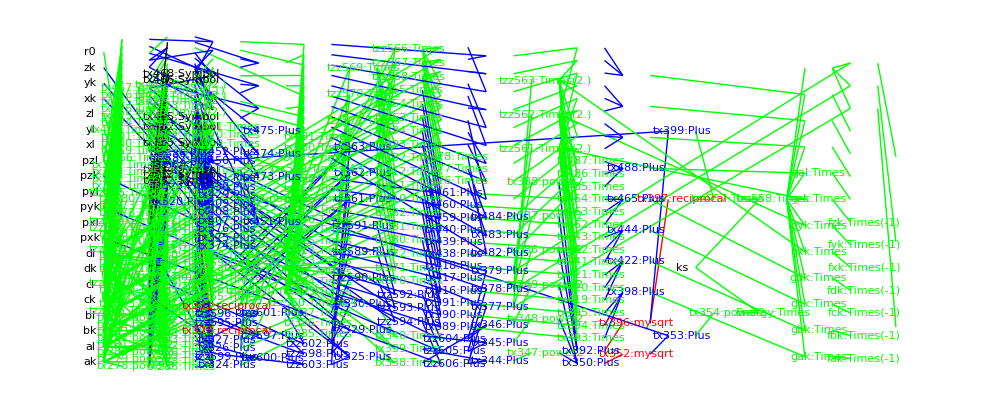

```mathematica
packGraph[cylrepPack]
```

```mathematica
cylrepPack[[4]]
```

Output→{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

# Nonbond rigid-body energy term

```mathematica
Clear[pm,pxm,pym,pzm];
Clear[pn,pxn,pyn,pzn];
Clear[evdw, eeel,nonbondRBEquation];
```

```mathematica
pm = { pxm,pym,pzm };
pn = { pxn,pyn,pzn };
```

```mathematica
plabm = quatmultrans[quat[am,bm,cm,dm],{xm,ym,zm},pm]
```

{pxm+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)+xm,pym+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)+ym,pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)+zm}

```mathematica
plabn = quatmultrans[quat[an,bn,cn,dn],{xn,yn,zn},pn]
```

{pxn+(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xn,pyn+(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+yn,pzn+(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zn}

```mathematica
nonbondRBDistance = Sqrt[(plabm-plabn).(plabm-plabn)]
```

√((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)

```mathematica
evdwEquation = (dA/nonbondRBDistance^12-dC/nonbondRBDistance^6)
```

dA/((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^6-dC/((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^3

```mathematica
eeelEquation = (dQ1Q2/nonbondRBDistance)
```

dQ1Q2/(√((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2))

```mathematica
nonbondRBEnergyFn = evdwEquation + eeelEquation
```

dA/((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^6-dC/((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2)^3+dQ1Q2/(√((pxm-pxn+(2. (-cm^2 pxm-dm^2 pxm+bm cm pym-am dm pym+am cm pzm+bm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (-cn^2 pxn-dn^2 pxn+bn cn pyn-an dn pyn+an cn pzn+bn dn pzn))/(an^2+bn^2+cn^2+dn^2)+xm-xn)^2+(pym-pyn+(2. (bm cm pxm+am dm pxm-bm^2 pym-dm^2 pym-am bm pzm+cm dm pzm))/(am^2+bm^2+cm^2+dm^2)-(2. (bn cn pxn+an dn pxn-bn^2 pyn-dn^2 pyn-an bn pzn+cn dn pzn))/(an^2+bn^2+cn^2+dn^2)+ym-yn)^2+(pzm+(2. (-am cm pxm+bm dm pxm+am bm pym+cm dm pym-bm^2 pzm-cm^2 pzm))/(am^2+bm^2+cm^2+dm^2)-pzn-(2. (-an cn pxn+bn dn pxn+an bn pyn+cn dn pyn-bn^2 pzn-cn^2 pzn))/(an^2+bn^2+cn^2+dn^2)+zm-zn)^2))

```mathematica
nonbondRBVarNames = { 
{am,a,I1,0},
{bm,b,I1,1},
{cm,c,I1,2},
{dm,d,I1,3},
{xm,x,I1,4},
{ym,y,I1,5},
{zm,z,I1,6},
{an,a,I2,0},
{bn,b,I2,1},
{cn,c,I2,2},
{dn,d,I2,3},
{xn,x,I2,4},
{yn,y,I2,5},
{zn,z,I2,6}
};
```

```mathematica
nonbondRBSetupRules = {};
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I1);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dQ1Q2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dA);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[nonbondRBVarNames],i++,
str = "NONBONDRB_SET_POSITION("<>ToString[nonbondRBVarNames[[i]][[1]]]<>","<>ToString[nonbondRBVarNames[[i]][[3]]]<>","<>ToString[nonbondRBVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[nonbondRBSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(xm,pointA,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(ym,pointA,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(zm,pointA,getZ());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(xn,pointB,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(yn,pointB,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(zn,pointB,getZ());"]];
```

```mathematica
nonbondRBSetupRules//MatrixForm
```

(CCode[NONBONDRB_SET_PARAMETER(I1);]
CCode[NONBONDRB_SET_PARAMETER(I2);]
CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]
CCode[NONBONDRB_SET_PARAMETER(dA);]
CCode[NONBONDRB_SET_PARAMETER(dC);]
CCode[NONBONDRB_SET_POSITION(am,I1,0);]
CCode[NONBONDRB_SET_POSITION(bm,I1,1);]
CCode[NONBONDRB_SET_POSITION(cm,I1,2);]
CCode[NONBONDRB_SET_POSITION(dm,I1,3);]
CCode[NONBONDRB_SET_POSITION(xm,I1,4);]
CCode[NONBONDRB_SET_POSITION(ym,I1,5);]
CCode[NONBONDRB_SET_POSITION(zm,I1,6);]
CCode[NONBONDRB_SET_POSITION(an,I2,0);]
CCode[NONBONDRB_SET_POSITION(bn,I2,1);]
CCode[NONBONDRB_SET_POSITION(cn,I2,2);]
CCode[NONBONDRB_SET_POSITION(dn,I2,3);]
CCode[NONBONDRB_SET_POSITION(xn,I2,4);]
CCode[NONBONDRB_SET_POSITION(yn,I2,5);]
CCode[NONBONDRB_SET_POSITION(zn,I2,6);]
CCode[NONBONDRB_SET_POINT(xm,pointA,getX());]
CCode[NONBONDRB_SET_POINT(ym,pointA,getY());]
CCode[NONBONDRB_SET_POINT(zm,pointA,getZ());]
CCode[NONBONDRB_SET_POINT(xn,pointB,getX());]
CCode[NONBONDRB_SET_POINT(yn,pointB,getY());]
CCode[NONBONDRB_SET_POINT(zn,pointB,getZ());])

```mathematica
nonbondRBEnergyRules = {};
nonbondRBOutputs = {};
AppendTo[nonbondRBEnergyRules,Assign[Energy,nonbondRBEnergyFn]];
AppendTo[nonbondRBEnergyRules,EnergyAccumulate["NONBONDRB",Energy]];
AppendTo[nonbondRBOutputs,Energy];
```

## Append the Gradient rules

```mathematica
nonbondRBForceRules = {};
```

```mathematica
AppendGradientAndForce["NONBONDRB",nonbondRBEnergyRules,nonbondRBOutputs,nonbondRBEnergyFn,nonbondRBVarNames];
```

```mathematica
nonbondRBOutputs
```

{Energy,fam,fbm,fcm,fdm,fxm,fym,fzm,fan,fbn,fcn,fdn,fxn,fyn,fzn}

### Collect terms and convert to C code

```mathematica
nonbondRBAllRules ={
nonbondRBSetupRules,
nonbondRBEnergyRules};
```

```mathematica
nonbondRBRules = Flatten[nonbondRBAllRules];
```

```mathematica
nonbondRBRules
```

{CCode[NONBONDRB_SET_PARAMETER(I1);],CCode[NONBONDRB_SET_PARAMETER(I2);],CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);],«64»,-gzn→fzn,CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]}

```mathematica
nonbondRBInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

```mathematica
AppendTo[nonbondRBOutputs,nonbondRBDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
nonbondRBPack0 = {
Name->"NONBONDRB",
AdditionalCDeclares->"",
DerivativeVariables->{ ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl },
Rules->nonbondRBRules,
Input->nonbondRBInput,
Output->nonbondRBOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[nonbondRBPack0];
```

Writing finite difference debug code to: _NONBONDRB_debugFiniteDifference.cc

Writing debug variable declares to: _NONBONDRB_debugEvalDeclares.cc

Writing xml output debug code to: _NONBONDRB_debugEvalSerialize.cc

Writing set variables debug code to: _NONBONDRB_debugEvalSet.cc

### Put the pedal to the metal and generate "C" code.

```mathematica
nonbondRBPack = packOptimize[nonbondRBPack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak bk -> tx224

-2. al bl -> tx225

-2. ak ck -> tx226

2. ak ck -> tx227

2. bk ck -> tx228

-2. al cl -> tx229

2. al cl -> tx230

2. bl cl -> tx231

-2. ak dk -> tx232

2. ak dk -> tx233

2. bk dk -> tx234

2. ck dk -> tx235

-2. al dl -> tx236

2. al dl -> tx237

2. bl dl -> tx238

2. cl dl -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-(tx247 xh2) -> tx265

-(tx254 xh2) -> tx266

-(tx255 xh2) -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-(tx253 yh2) -> tx272

-(tx257 yh2) -> tx273

-(tx261 yh2) -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-(tx256 zh2) -> tx279

-(tx257 zh2) -> tx280

-(tx259 zh2) -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

powern2[tx289] -> tx439

reciprocal[tx289] -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak xh1 -> tx296

-2. ck xh1 -> tx297

2. dk xh1 -> tx298

2. ak yh1 -> tx299

-2. bk yh1 -> tx300

-2. dk yh1 -> tx301

2. ak zh1 -> tx302

-2. bk zh1 -> tx303

2. ck zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 tx305 -> tx308

2. tx284 tx306 -> tx309

2. tx283 tx307 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

-6. dA tx311 tx314 -> tx315

3 dC tx312 tx314 -> tx316

-0.5 dQ1Q2 tx313 tx314 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk xh1 -> tx318

2. ck xh1 -> tx319

-2. ak yh1 -> tx320

2. ck yh1 -> tx321

-2. ak zh1 -> tx322

2. dk zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

2. tx285 tx324 -> tx327

2. tx284 tx325 -> tx328

2. tx283 tx326 -> tx329

tx327 + tx328 + tx329 -> tx330

-6. dA tx311 tx330 -> tx331

3 dC tx312 tx330 -> tx332

-0.5 dQ1Q2 tx313 tx330 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

-2. ak xh1 -> tx334

2. bk yh1 -> tx335

2. dk yh1 -> tx336

-2. ck zh1 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

2. tx284 tx326 -> tx340

2. tx283 tx338 -> tx341

2. tx285 tx339 -> tx342

tx340 + tx341 + tx342 -> tx343

-6. dA tx311 tx343 -> tx344

3 dC tx312 tx343 -> tx345

-0.5 dQ1Q2 tx313 tx343 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

2. bk zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

2. tx284 tx307 -> tx349

2. tx285 tx326 -> tx350

2. tx283 tx348 -> tx351

tx349 + tx350 + tx351 -> tx352

-6. dA tx311 tx352 -> tx353

3 dC tx312 tx352 -> tx354

-0.5 dQ1Q2 tx313 tx352 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. dA tx283 tx311 -> tx356

6. dC tx283 tx312 -> tx357

-(dQ1Q2 tx283 tx313) -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

-12. dA tx284 tx311 -> tx359

6. dC tx284 tx312 -> tx360

-(dQ1Q2 tx284 tx313) -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

-12. dA tx285 tx311 -> tx362

6. dC tx285 tx312 -> tx363

-(dQ1Q2 tx285 tx313) -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

-2. al xh2 -> tx365

2. cl xh2 -> tx366

-2. dl xh2 -> tx367

-2. al yh2 -> tx368

2. bl yh2 -> tx369

2. dl yh2 -> tx370

-2. al zh2 -> tx371

2. bl zh2 -> tx372

-2. cl zh2 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

2. tx285 tx374 -> tx377

2. tx284 tx375 -> tx378

2. tx283 tx376 -> tx379

tx377 + tx378 + tx379 -> tx380

-6. dA tx311 tx380 -> tx381

3 dC tx312 tx380 -> tx382

-0.5 dQ1Q2 tx313 tx380 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

-2. bl xh2 -> tx384

-2. cl xh2 -> tx385

2. al yh2 -> tx386

-2. cl yh2 -> tx387

2. al zh2 -> tx388

-2. dl zh2 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

2. tx285 tx390 -> tx393

2. tx284 tx391 -> tx394

2. tx283 tx392 -> tx395

tx393 + tx394 + tx395 -> tx396

-6. dA tx311 tx396 -> tx397

3 dC tx312 tx396 -> tx398

-0.5 dQ1Q2 tx313 tx396 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

2. al xh2 -> tx400

-2. bl yh2 -> tx401

-2. dl yh2 -> tx402

2. cl zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

2. tx284 tx392 -> tx406

2. tx283 tx404 -> tx407

2. tx285 tx405 -> tx408

tx406 + tx407 + tx408 -> tx409

-6. dA tx311 tx409 -> tx410

3 dC tx312 tx409 -> tx411

-0.5 dQ1Q2 tx313 tx409 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

-2. bl zh2 -> tx413

tx367 + tx386 + tx413 -> tx414

2. tx284 tx376 -> tx415

2. tx285 tx392 -> tx416

2. tx283 tx414 -> tx417

tx415 + tx416 + tx417 -> tx418

-6. dA tx311 tx418 -> tx419

3 dC tx312 tx418 -> tx420

-0.5 dQ1Q2 tx313 tx418 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. dA tx283 tx311 -> tx422

-6. dC tx283 tx312 -> tx423

dQ1Q2 tx283 tx313 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

12. dA tx284 tx311 -> tx425

-6. dC tx284 tx312 -> tx426

dQ1Q2 tx284 tx313 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

12. dA tx285 tx311 -> tx428

-6. dC tx285 tx312 -> tx429

dQ1Q2 tx285 tx313 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

power2[reciprocal[tx289]] -> tx439

reciprocal[tx289] -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx367 + tx386 + tx413 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tx472 -> tx440, tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx472 -> tx440

tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

reciprocal[tx289] -> tx472

power2[tx472] -> tx439

tx472 -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx367 + tx386 + tx413 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tx472 -> tx440, tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx472 -> tx440

tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx222 + tx240 -> tzz476

tx220 + tx242 + tzz476 -> tx258

tx223 + tx241 -> tzz475

tx221 + tx243 + tzz475 -> tx259

tx218 + tx244 + tzz476 -> tx260

tx219 + tx245 + tzz475 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

reciprocal[tx289] -> tx472

power2[tx472] -> tx439

tx472 -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx320 -> tzz474

tx303 + tzz474 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx347 + tzz474 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx386 -> tzz473

tx372 + tzz473 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx413 + tzz473 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "NONBONDRB", AdditionalCDeclares → "", DerivativeVariables → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Rules → {CCode["NONBONDRB_SET_PARAMETER(I1);"], CCode["NONBONDRB_SET_PARAMETER(I2);"], CCode["NONBONDRB_SET_PARAMETER(dQ1Q2);"], CCode["NONBONDRB_SET_PARAMETER(dA);"], « 43 », CCode["NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );"], -6\ dA\ Plus[« 3 »]\ Power[« 2 »] + 3\ dC\ Plus[« 3 »]\ Power[« 2 »] - 1/2\ dQ1Q2\ Plus[« 3 »]\ Power[« 2 »] → gan, -gan → fan, « 19 »}, Input → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Output → {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx655 -> tx645, tx441 -> tx651}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tx655 -> tx645

tx441 -> tx651

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(xm,pointA,getX());]

CCode[NONBONDRB_SET_POINT(ym,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zm,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xn,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yn,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zn,pointB,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-(am cm pxm) -> tx330

bm cm pxm -> tx331

am dm pxm -> tx332

bm dm pxm -> tx333

-(an cn pxn) -> tx334

bn cn pxn -> tx335

an dn pxn -> tx336

bn dn pxn -> tx337

am bm pym -> tx338

bm cm pym -> tx339

-(am dm pym) -> tx340

cm dm pym -> tx341

an bn pyn -> tx342

bn cn pyn -> tx343

-(an dn pyn) -> tx344

cn dn pyn -> tx345

-(am bm pzm) -> tx346

am cm pzm -> tx347

bm dm pzm -> tx348

cm dm pzm -> tx349

-(an bn pzn) -> tx350

an cn pzn -> tx351

bn dn pzn -> tx352

cn dn pzn -> tx353

-(pym tx324) -> tx354

-(pzm tx324) -> tx355

-(pyn tx325) -> tx356

-(pzn tx325) -> tx357

-(pxm tx326) -> tx358

-(pzm tx326) -> tx359

-(pxn tx327) -> tx360

-(pzn tx327) -> tx361

-(pxm tx328) -> tx362

-(pym tx328) -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

-(pxn tx329) -> tx365

-(pyn tx329) -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

-pxn -> tx376

-pyn -> tx377

-pzn -> tx378

2. tx368 tx372 -> tx379

2. tx370 tx372 -> tx380

2. tx371 tx372 -> tx381

-2. tx369 tx375 -> tx382

-2. tx373 tx375 -> tx383

-2. tx374 tx375 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

powern2[tx394] -> tx654

reciprocal[tx394] -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

-(cm pxm) -> tx407

dm pxm -> tx408

bm pym -> tx409

-(dm pym) -> tx410

-(bm pzm) -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

-2. tx375 tx413 -> tx420

-2. tx375 tx414 -> tx421

-2. tx375 tx415 -> tx422

-4. am tx368 tx416 -> tx423

-4. am tx370 tx416 -> tx424

-4. am tx371 tx416 -> tx425

2. tx372 tx417 -> tx426

2. tx372 tx418 -> tx427

2. tx372 tx419 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 tx432 -> tx438

2. tx430 tx433 -> tx439

2. tx429 tx434 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

powern2[tx441] -> tx656

reciprocal[tx441] -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

-6. dA tx442 tx443 -> tx446

3 dC tx442 tx444 -> tx447

-0.5 dQ1Q2 tx442 tx445 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

cm pym -> tx451

-(am pzm) -> tx452

-2. bm pzm -> tx453

dm pzm -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

-4. bm tx368 tx416 -> tx459

-4. bm tx370 tx416 -> tx460

-4. bm tx371 tx416 -> tx461

2. tx372 tx456 -> tx462

2. tx372 tx457 -> tx463

2. tx372 tx458 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

2. tx431 tx465 -> tx468

2. tx429 tx466 -> tx469

2. tx430 tx467 -> tx470

tx468 + tx469 + tx470 -> tx471

-6. dA tx443 tx471 -> tx472

3 dC tx444 tx471 -> tx473

-0.5 dQ1Q2 tx445 tx471 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

-(am pxm) -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

-4. cm tx368 tx416 -> tx484

-4. cm tx370 tx416 -> tx485

-4. cm tx371 tx416 -> tx486

2. tx372 tx481 -> tx487

2. tx372 tx482 -> tx488

2. tx372 tx483 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

2. tx430 tx490 -> tx493

2. tx431 tx491 -> tx494

2. tx429 tx492 -> tx495

tx493 + tx494 + tx495 -> tx496

-6. dA tx443 tx496 -> tx497

3 dC tx444 tx496 -> tx498

-0.5 dQ1Q2 tx445 tx496 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

-4. dm tx368 tx416 -> tx508

-4. dm tx370 tx416 -> tx509

-4. dm tx371 tx416 -> tx510

2. tx372 tx505 -> tx511

2. tx372 tx506 -> tx512

2. tx372 tx507 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

2. tx431 tx514 -> tx517

2. tx429 tx515 -> tx518

2. tx430 tx516 -> tx519

tx517 + tx518 + tx519 -> tx520

-6. dA tx443 tx520 -> tx521

3 dC tx444 tx520 -> tx522

-0.5 dQ1Q2 tx445 tx520 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. dA tx429 tx443 -> tx524

6. dC tx429 tx444 -> tx525

-(dQ1Q2 tx429 tx445) -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

-12. dA tx430 tx443 -> tx527

6. dC tx430 tx444 -> tx528

-(dQ1Q2 tx430 tx445) -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

-12. dA tx431 tx443 -> tx530

6. dC tx431 tx444 -> tx531

-(dQ1Q2 tx431 tx445) -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

dn pxn -> tx533

bn pyn -> tx534

cn pzn -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. an tx413 tx539 -> tx543

4. an tx414 tx539 -> tx544

4. an tx415 tx539 -> tx545

-2. tx375 tx540 -> tx546

-2. tx375 tx541 -> tx547

-2. tx375 tx542 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

2. tx431 tx549 -> tx552

2. tx429 tx550 -> tx553

2. tx430 tx551 -> tx554

tx552 + tx553 + tx554 -> tx555

-6. dA tx443 tx555 -> tx556

3 dC tx444 tx555 -> tx557

-0.5 dQ1Q2 tx445 tx555 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

cn pyn -> tx561

-2. bn pzn -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

4. bn tx413 tx539 -> tx569

4. bn tx414 tx539 -> tx570

4. bn tx415 tx539 -> tx571

-2. tx375 tx566 -> tx572

-2. tx375 tx567 -> tx573

-2. tx375 tx568 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

2. tx431 tx575 -> tx578

2. tx429 tx576 -> tx579

2. tx430 tx577 -> tx580

tx578 + tx579 + tx580 -> tx581

-6. dA tx443 tx581 -> tx582

3 dC tx444 tx581 -> tx583

-0.5 dQ1Q2 tx445 tx581 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

4. cn tx413 tx539 -> tx594

4. cn tx414 tx539 -> tx595

4. cn tx415 tx539 -> tx596

-2. tx375 tx591 -> tx597

-2. tx375 tx592 -> tx598

-2. tx375 tx593 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

2. tx430 tx600 -> tx603

2. tx431 tx601 -> tx604

2. tx429 tx602 -> tx605

tx603 + tx604 + tx605 -> tx606

-6. dA tx443 tx606 -> tx607

3 dC tx444 tx606 -> tx608

-0.5 dQ1Q2 tx445 tx606 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

bn pzn -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

4. dn tx413 tx539 -> tx618

4. dn tx414 tx539 -> tx619

4. dn tx415 tx539 -> tx620

-2. tx375 tx615 -> tx621

-2. tx375 tx616 -> tx622

-2. tx375 tx617 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

2. tx431 tx624 -> tx627

2. tx429 tx625 -> tx628

2. tx430 tx626 -> tx629

tx627 + tx628 + tx629 -> tx630

-6. dA tx443 tx630 -> tx631

3 dC tx444 tx630 -> tx632

-0.5 dQ1Q2 tx445 tx630 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. dA tx429 tx443 -> tx634

-6. dC tx429 tx444 -> tx635

dQ1Q2 tx429 tx445 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

12. dA tx430 tx443 -> tx637

-6. dC tx430 tx444 -> tx638

dQ1Q2 tx430 tx445 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

12. dA tx431 tx443 -> tx640

-6. dC tx431 tx444 -> tx641

dQ1Q2 tx431 tx445 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx655 -> tx645, tzz690 -> tx408, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx655 -> tx645

tzz690 -> tx408

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(xm,pointA,getX());]

CCode[NONBONDRB_SET_POINT(ym,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zm,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xn,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yn,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zn,pointB,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

power2[reciprocal[tx394]] -> tx654

reciprocal[tx394] -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

power2[reciprocal[tx441]] -> tx656

reciprocal[tx441] -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

eliminateTrivialRules

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx697 -> tx655, tx655 -> tx645, tzz690 -> tx408, tx698 -> tx657, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx697 -> tx655

tx655 -> tx645

tzz690 -> tx408

tx698 -> tx657

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(xm,pointA,getX());]

CCode[NONBONDRB_SET_POINT(ym,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zm,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xn,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yn,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zn,pointB,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx334 + tx337 + tx342 + tx345 + tx357 + tx361 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx343 + tx344 + tx351 + tx352 + tx360 + tx365 -> tx373

tx335 + tx336 + tx350 + tx353 + tx356 + tx366 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

pxm + tx376 + tx380 + tx383 + tx385 + xm -> tx388

pym + tx377 + tx381 + tx384 + tx386 + ym -> tx389

pzm + tx378 + tx379 + tx382 + tx387 + zm -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

reciprocal[tx394] -> tx697

power2[tx697] -> tx654

tx697 -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx343 + tx344 + tx351 + tx352 + tx401 + tx402 -> tx413

tx335 + tx336 + tx350 + tx353 + tx403 + tx404 -> tx414

tx334 + tx337 + tx342 + tx345 + tx405 + tx406 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

pxm + tx376 + tx380 + tx385 + tx420 + xm -> tx429

pym + tx377 + tx381 + tx386 + tx421 + ym -> tx430

pzm + tx378 + tx379 + tx387 + tx422 + zm -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

reciprocal[tx441] -> tx698

power2[tx698] -> tx656

tx698 -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

trivialRules>> triv = {tzz685 -> tx376, tzz684 -> tx377, tzz696 -> tx378, tx697 -> tx655, tx655 -> tx645, tzz690 -> tx408, tx698 -> tx657, tx441 -> tx651, tzz693 -> tx451, tzz689 -> tx454, tzz688 -> tx533, tzz691 -> tx535, tzz692 -> tx561, tzz680 -> tx611}

trivialRules>> outs = {Energy, fam, fbm, fcm, fdm, fxm, fym, fzm, fan, fbn, fcn, fdn, fxn, fyn, fzn, nonbondRBDeviation}

Trivial rules are being removed: tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

tx697 -> tx655

tx655 -> tx645

tzz690 -> tx408

tx698 -> tx657

tx441 -> tx651

tzz693 -> tx451

tzz689 -> tx454

tzz688 -> tx533

tzz691 -> tx535

tzz692 -> tx561

tzz680 -> tx611

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(am,I1,0);]

CCode[NONBONDRB_SET_POSITION(bm,I1,1);]

CCode[NONBONDRB_SET_POSITION(cm,I1,2);]

CCode[NONBONDRB_SET_POSITION(dm,I1,3);]

CCode[NONBONDRB_SET_POSITION(xm,I1,4);]

CCode[NONBONDRB_SET_POSITION(ym,I1,5);]

CCode[NONBONDRB_SET_POSITION(zm,I1,6);]

CCode[NONBONDRB_SET_POSITION(an,I2,0);]

CCode[NONBONDRB_SET_POSITION(bn,I2,1);]

CCode[NONBONDRB_SET_POSITION(cn,I2,2);]

CCode[NONBONDRB_SET_POSITION(dn,I2,3);]

CCode[NONBONDRB_SET_POSITION(xn,I2,4);]

CCode[NONBONDRB_SET_POSITION(yn,I2,5);]

CCode[NONBONDRB_SET_POSITION(zn,I2,6);]

CCode[NONBONDRB_SET_POINT(xm,pointA,getX());]

CCode[NONBONDRB_SET_POINT(ym,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zm,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xn,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yn,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zn,pointB,getZ());]

power2[am] -> tx322

power2[an] -> tx323

power2[bm] -> tx324

power2[bn] -> tx325

power2[cm] -> tx326

power2[cn] -> tx327

power2[dm] -> tx328

power2[dn] -> tx329

-pxm -> tzz672

am cm -> tzz694

tzz672 tzz694 -> tx330

bm cm pxm -> tx331

dm pxm -> tzz690

am tzz690 -> tx332

bm tzz690 -> tx333

-pxn -> tzz685

an cn tzz685 -> tx334

bn cn pxn -> tx335

dn pxn -> tzz688

an tzz688 -> tx336

bn tzz688 -> tx337

am bm -> tzz695

pym tzz695 -> tx338

cm pym -> tzz693

bm tzz693 -> tx339

-pym -> tzz679

am dm tzz679 -> tx340

dm tzz693 -> tx341

an bn pyn -> tx342

cn pyn -> tzz692

bn tzz692 -> tx343

-pyn -> tzz684

an dn tzz684 -> tx344

dn tzz692 -> tx345

-pzm -> tzz671

tzz671 tzz695 -> tx346

pzm tzz694 -> tx347

dm pzm -> tzz689

bm tzz689 -> tx348

cm tzz689 -> tx349

bn pzn -> tzz680

-(an tzz680) -> tx350

cn pzn -> tzz691

an tzz691 -> tx351

dn tzz680 -> tx352

dn tzz691 -> tx353

tx324 tzz679 -> tx354

tx324 tzz671 -> tx355

tx325 tzz684 -> tx356

-pzn -> tzz696

tx325 tzz696 -> tx357

tx326 tzz672 -> tx358

tx326 tzz671 -> tx359

tx327 tzz685 -> tx360

tx327 tzz696 -> tx361

tx328 tzz672 -> tx362

tx328 tzz679 -> tx363

tx322 + tx324 + tx326 + tx328 -> tx364

tx329 tzz685 -> tx365

tx329 tzz684 -> tx366

tx323 + tx325 + tx327 + tx329 -> tx367

tx330 + tx333 + tx338 + tx341 + tx355 + tx359 -> tx368

tx342 + tx345 -> tzz712

tx337 + tzz712 -> tzz713

tx334 + tzz713 -> tzz716

tx357 + tx361 + tzz716 -> tx369

tx339 + tx340 + tx347 + tx348 + tx358 + tx362 -> tx370

tx331 + tx332 + tx346 + tx349 + tx354 + tx363 -> tx371

reciprocal[tx364] -> tx372

tx351 + tx352 -> tzz708

tx344 + tzz708 -> tzz710

tx343 + tzz710 -> tzz711

tx360 + tx365 + tzz711 -> tx373

tx350 + tx353 -> tzz709

tx336 + tzz709 -> tzz714

tx335 + tzz714 -> tzz715

tx356 + tx366 + tzz715 -> tx374

reciprocal[tx367] -> tx375

tzz685 -> tx376

tzz684 -> tx377

tzz696 -> tx378

2. tx372 -> tzz659

tx368 tzz659 -> tx379

tx370 tzz659 -> tx380

tx371 tzz659 -> tx381

-2. tx375 -> tzz658

tx369 tzz658 -> tx382

tx373 tzz658 -> tx383

tx374 tzz658 -> tx384

-xn -> tx385

-yn -> tx386

-zn -> tx387

tx385 + xm -> tzz701

tx380 + tzz701 -> tzz703

tx376 + tzz703 -> tzz707

pxm + tzz707 -> tzz719

tx383 + tzz719 -> tx388

tx386 + ym -> tzz700

tx381 + tzz700 -> tzz702

tx377 + tzz702 -> tzz706

pym + tzz706 -> tzz718

tx384 + tzz718 -> tx389

tx387 + zm -> tzz699

tx379 + tzz699 -> tzz704

tx378 + tzz704 -> tzz705

pzm + tzz705 -> tzz717

tx382 + tzz717 -> tx390

power2[tx388] -> tx391

power2[tx389] -> tx392

power2[tx390] -> tx393

tx391 + tx392 + tx393 -> tx394

reciprocal[tx394] -> tx697

power2[tx697] -> tx654

tx697 -> tx655

tx654 tx655 -> tx643

power2[tx643] -> tx395

power2[tx655] -> tx644

tx655 -> tx645

tx644 tx645 -> tx396

mysqrt[tx394] -> tx646

reciprocal[tx646] -> tx397

dA tx395 -> tx398

-(dC tx396) -> tx399

dQ1Q2 tx397 -> tx400

tx398 + tx399 + tx400 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

tx327 tx376 -> tx401

tx329 tx376 -> tx402

tx325 tx377 -> tx403

tx329 tx377 -> tx404

tx325 tx378 -> tx405

tx327 tx378 -> tx406

cm tzz672 -> tx407

tzz690 -> tx408

bm pym -> tx409

dm tzz679 -> tx410

bm tzz671 -> tx411

cm pzm -> tx412

tx401 + tx402 + tzz711 -> tx413

tx403 + tx404 + tzz715 -> tx414

tx405 + tx406 + tzz716 -> tx415

power2[tx372] -> tx416

tx407 + tx409 -> tx417

tx408 + tx411 -> tx418

tx410 + tx412 -> tx419

tx413 tzz658 -> tx420

tx414 tzz658 -> tx421

tx415 tzz658 -> tx422

-4. tx416 -> tzz664

tx368 tzz664 -> tzz678

am tzz678 -> tx423

tx370 tzz664 -> tzz677

am tzz677 -> tx424

tx371 tzz664 -> tzz676

am tzz676 -> tx425

tx417 tzz659 -> tx426

tx418 tzz659 -> tx427

tx419 tzz659 -> tx428

tx420 + tzz719 -> tx429

tx421 + tzz718 -> tx430

tx422 + tzz717 -> tx431

tx423 + tx426 -> tx432

tx425 + tx427 -> tx433

tx424 + tx428 -> tx434

power2[tx429] -> tx435

power2[tx430] -> tx436

power2[tx431] -> tx437

2. tx431 -> tzz666

tx432 tzz666 -> tx438

2. tx430 -> tzz667

tx433 tzz667 -> tx439

2. tx429 -> tzz668

tx434 tzz668 -> tx440

tx435 + tx436 + tx437 -> tx441

tx438 + tx439 + tx440 -> tx442

reciprocal[tx441] -> tx698

power2[tx698] -> tx656

tx698 -> tx657

tx656 tx657 -> tx647

power2[tx656] -> tx648

tx647 tx648 -> tx443

power2[tx657] -> tx649

power2[tx649] -> tx444

mysqrt[tx441] -> tx650

tx441 -> tx651

reciprocal[tx650] -> tx652

reciprocal[tx651] -> tx653

tx652 tx653 -> tx445

dA tx443 -> tzz662

-6. tzz662 -> tzz670

tx442 tzz670 -> tx446

dC tx444 -> tzz661

3 tzz661 -> tzz665

tx442 tzz665 -> tx447

dQ1Q2 tx445 -> tzz660

-0.5 tzz660 -> tzz669

tx442 tzz669 -> tx448

tx446 + tx447 + tx448 -> gam

-gam -> fam

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fam );]

cm pxm -> tx449

am pym -> tx450

tzz693 -> tx451

am tzz671 -> tx452

-2. bm pzm -> tx453

tzz689 -> tx454

-2. tx409 -> tx455

tx408 + tx450 + tx453 -> tx456

tx451 + tx454 -> tx457

tx449 + tx452 + tx455 -> tx458

bm tzz678 -> tx459

bm tzz677 -> tx460

bm tzz676 -> tx461

tx456 tzz659 -> tx462

tx457 tzz659 -> tx463

tx458 tzz659 -> tx464

tx459 + tx462 -> tx465

tx460 + tx463 -> tx466

tx461 + tx464 -> tx467

tx465 tzz666 -> tx468

tx466 tzz668 -> tx469

tx467 tzz667 -> tx470

tx468 + tx469 + tx470 -> tx471

tx471 tzz670 -> tx472

tx471 tzz665 -> tx473

tx471 tzz669 -> tx474

tx472 + tx473 + tx474 -> gbm

-gbm -> fbm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbm );]

am tzz672 -> tx475

bm pxm -> tx476

dm pym -> tx477

am pzm -> tx478

-2. tx412 -> tx479

-2. tx449 -> tx480

tx454 + tx476 -> tx481

tx475 + tx477 + tx479 -> tx482

tx409 + tx478 + tx480 -> tx483

cm tzz678 -> tx484

cm tzz677 -> tx485

cm tzz676 -> tx486

tx481 tzz659 -> tx487

tx482 tzz659 -> tx488

tx483 tzz659 -> tx489

tx486 + tx487 -> tx490

tx484 + tx488 -> tx491

tx485 + tx489 -> tx492

tx490 tzz667 -> tx493

tx491 tzz666 -> tx494

tx492 tzz668 -> tx495

tx493 + tx494 + tx495 -> tx496

tx496 tzz670 -> tx497

tx496 tzz665 -> tx498

tx496 tzz669 -> tx499

tx497 + tx498 + tx499 -> gcm

-gcm -> fcm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fcm );]

am pxm -> tx500

bm pzm -> tx501

-2. tx408 -> tx502

-tx450 -> tx503

-2. tx477 -> tx504

tx451 + tx476 -> tx505

tx501 + tx502 + tx503 -> tx506

tx412 + tx500 + tx504 -> tx507

dm tzz678 -> tx508

dm tzz677 -> tx509

dm tzz676 -> tx510

tx505 tzz659 -> tx511

tx506 tzz659 -> tx512

tx507 tzz659 -> tx513

tx508 + tx511 -> tx514

tx509 + tx512 -> tx515

tx510 + tx513 -> tx516

tx514 tzz666 -> tx517

tx515 tzz668 -> tx518

tx516 tzz667 -> tx519

tx517 + tx518 + tx519 -> tx520

tx520 tzz670 -> tx521

tx520 tzz665 -> tx522

tx520 tzz669 -> tx523

tx521 + tx522 + tx523 -> gdm

-gdm -> fdm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdm );]

-12. tzz662 -> tzz687

tx429 tzz687 -> tx524

6. tzz661 -> tzz682

tx429 tzz682 -> tx525

-tzz660 -> tzz683

tx429 tzz683 -> tx526

tx524 + tx525 + tx526 -> gxm

-gxm -> fxm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxm );]

tx430 tzz687 -> tx527

tx430 tzz682 -> tx528

tx430 tzz683 -> tx529

tx527 + tx528 + tx529 -> gym

-gym -> fym

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fym );]

tx431 tzz687 -> tx530

tx431 tzz682 -> tx531

tx431 tzz683 -> tx532

tx530 + tx531 + tx532 -> gzm

-gzm -> fzm

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzm );]

tzz688 -> tx533

bn pyn -> tx534

tzz691 -> tx535

cn tx376 -> tx536

dn tx377 -> tx537

bn tx378 -> tx538

power2[tx375] -> tx539

tx534 + tx536 -> tx540

tx535 + tx537 -> tx541

tx533 + tx538 -> tx542

4. tx539 -> tzz663

tx413 tzz663 -> tzz675

an tzz675 -> tx543

tx414 tzz663 -> tzz674

an tzz674 -> tx544

tx415 tzz663 -> tzz673

an tzz673 -> tx545

tx540 tzz658 -> tx546

tx541 tzz658 -> tx547

tx542 tzz658 -> tx548

tx545 + tx546 -> tx549

tx543 + tx547 -> tx550

tx544 + tx548 -> tx551

tx549 tzz666 -> tx552

tx550 tzz668 -> tx553

tx551 tzz667 -> tx554

tx552 + tx553 + tx554 -> tx555

tx555 tzz670 -> tx556

tx555 tzz665 -> tx557

tx555 tzz669 -> tx558

tx556 + tx557 + tx558 -> gan

-gan -> fan

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fan );]

cn pxn -> tx559

an pyn -> tx560

tzz692 -> tx561

-2. tzz680 -> tx562

dn pzn -> tx563

an tx378 -> tx564

-2. tx534 -> tx565

tx533 + tx560 + tx562 -> tx566

tx561 + tx563 -> tx567

tx559 + tx564 + tx565 -> tx568

bn tzz675 -> tx569

bn tzz674 -> tx570

bn tzz673 -> tx571

tx566 tzz658 -> tx572

tx567 tzz658 -> tx573

tx568 tzz658 -> tx574

tx571 + tx572 -> tx575

tx569 + tx573 -> tx576

tx570 + tx574 -> tx577

tx575 tzz666 -> tx578

tx576 tzz668 -> tx579

tx577 tzz667 -> tx580

tx578 + tx579 + tx580 -> tx581

tx581 tzz670 -> tx582

tx581 tzz665 -> tx583

tx581 tzz669 -> tx584

tx582 + tx583 + tx584 -> gbn

-gbn -> fbn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbn );]

bn pxn -> tx585

dn pyn -> tx586

an pzn -> tx587

an tx376 -> tx588

-2. tx535 -> tx589

-2. tx559 -> tx590

tx563 + tx585 -> tx591

tx586 + tx588 + tx589 -> tx592

tx534 + tx587 + tx590 -> tx593

cn tzz675 -> tx594

cn tzz674 -> tx595

cn tzz673 -> tx596

tx591 tzz658 -> tx597

tx592 tzz658 -> tx598

tx593 tzz658 -> tx599

tx595 + tx597 -> tx600

tx596 + tx598 -> tx601

tx594 + tx599 -> tx602

tx600 tzz667 -> tx603

tx601 tzz666 -> tx604

tx602 tzz668 -> tx605

tx603 + tx604 + tx605 -> tx606

tx606 tzz670 -> tx607

tx606 tzz665 -> tx608

tx606 tzz669 -> tx609

tx607 + tx608 + tx609 -> gcn

-gcn -> fcn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcn );]

an pxn -> tx610

tzz680 -> tx611

an tx377 -> tx612

-2. tx533 -> tx613

-2. tx586 -> tx614

tx561 + tx585 -> tx615

tx611 + tx612 + tx613 -> tx616

tx535 + tx610 + tx614 -> tx617

dn tzz675 -> tx618

dn tzz674 -> tx619

dn tzz673 -> tx620

tx615 tzz658 -> tx621

tx616 tzz658 -> tx622

tx617 tzz658 -> tx623

tx620 + tx621 -> tx624

tx618 + tx622 -> tx625

tx619 + tx623 -> tx626

tx624 tzz666 -> tx627

tx625 tzz668 -> tx628

tx626 tzz667 -> tx629

tx627 + tx628 + tx629 -> tx630

tx630 tzz670 -> tx631

tx630 tzz665 -> tx632

tx630 tzz669 -> tx633

tx631 + tx632 + tx633 -> gdn

-gdn -> fdn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdn );]

12. tzz662 -> tzz681

tx429 tzz681 -> tx634

-6. tzz661 -> tzz686

tx429 tzz686 -> tx635

tx429 tzz660 -> tx636

tx634 + tx635 + tx636 -> gxn

-gxn -> fxn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxn );]

tx430 tzz681 -> tx637

tx430 tzz686 -> tx638

tx430 tzz660 -> tx639

tx637 + tx638 + tx639 -> gyn

-gyn -> fyn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyn );]

tx431 tzz681 -> tx640

tx431 tzz686 -> tx641

tx431 tzz660 -> tx642

tx640 + tx641 + tx642 -> gzn

-gzn -> fzn

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzn );]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Collecting terms

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Writing declares to file: _NONBOND_termDeclares.cc

Writing code to file: _NONBOND_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

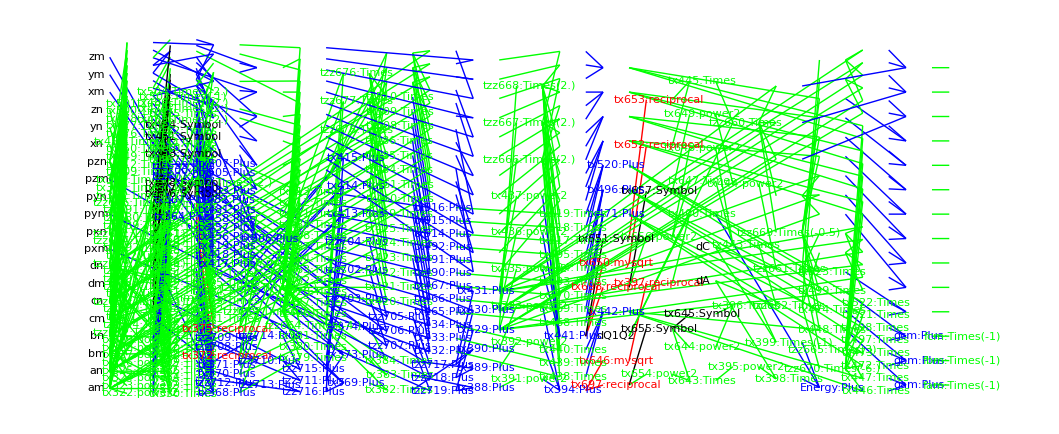

```mathematica
packGraph[nonbondRBPack]
```